# Теория

## Способ найти параметры (точечно)

## Одномерный случай

### Формулировка задачи

Рассмотрим систему линейных уравнений в матричнов виде

Y=X.A

где X∈ℝ^(n×m) , Y∈ℝ^n,A∈ℝ^m

Необходимо определить вектор A,зная X и Y .

### Простейщий случай

Если n=m и матрица X – невырожденная (det X ≠0),то вектор A определить точно

A=X^-1.Y

X^-1 – существует в силу невырожденности матрицы X

Проблема в том, что для матрицы X может не выполнятся n=mи она так же может быть вырожденной.

### Метод наименьших квадратов Linear Least Squares (LLS)

#### Функция ошибки

Для сравнения того,на сколько хорошо разные вектора A_1 и A_2  удовлетворяют уравнению (1),введём функцию ошибки φ

φ[A]=||Y-X.A||,

где ||Y||=√(∑_(i=1)^n Y_i^2)– евклидова норма в ℝ^n

#### Задача минимизации

Сформулируем задачу минимизации

{φ[A]⟶ min
A∈ℝ^m

Эта задача эквивалентна следующей

{φ^2[A]⟶ min
A∈ℝ^m

#### Решение

φ^2[A]=∑_(i=1)^n (Y_i-∑_(j=1)^m X_(i,j)A_j)^2

∂_A_k φ^2[A]=∑_(i=1)^n 2(Y_i-∑_(j=1)^m X_(i,j)A_j)(-X_(i,k))=2(Y-X.A)^T.X^k==0      ∀k=OverBar[1,m]

где X^k – k-ый стобец матрицы X

(Y-X.A)^T.X^k==0     ∀k=OverBar[1,m]

(Y-X.A)^T.X==𝟘_m^T

где 𝟘_m – нулевой вектор из ℝ^m

X^T.(Y-X.A)==𝟘_m

X^T.X.A==X^T.Y

A==(X^T.X)^-1 X^T.Y

проверка глобального минимума

∀h∈ℝ^m ≠0

φ^2[A+h]=<Y-X.(A+h),Y-X.(A+h)> =

<Y-X.A,Y-X.(A+h)>+<Y-X.h,Y-X.(A+h)> =

<Y-X.A,Y-X.A>+2<Y-X.A,X.h>+<X.h,X.h>

φ[A]≤φ[A+h]

Проблема в том,что  матрица X^T.X может быть вырожденной.

### Principle Components Regression (PCR)

Для того, чтобы обойти вырожденный случай матрицы X^T.X, в данном алгоритме аппроксимируют матрицу X матрицей X_a, получаемую из a первых главных компонент.

Так при помощи сингулярного разложения матрицы X получаем представление

X=U.S.V^T

где U∈ℝ^(n×n),S∈ℝ^(n×m),V∈ℝ^(m×m), причём U и V – ортогональные матрицы.

Тогда X_a можно представить в виде

X_a=U_a.S_a.V_a^T

где U_a∈ℝ^(n×a) – матрица, состоящая из первых a столбцов матрицы U ,
S∈ℝ^(a×a)– матрица, состоящая из первых a столбцов и строк  матрицы S,
V∈ℝ^(m×a)– матрица, состоящая из первых a столбцов матрицы V.

В случае, когда n=m и a=m, вектор A можно вычислить следующим образом

X_a=(U_a S_a)V_a^T=T P^T

где T=U_a S_a – остаётся ортогональной (т.е. T^T=T^-1)

(X_a.X_a^T)^-1.X_a^T=(T.P^T.(T.P^T)^T)^-1.(T.P^T)^T=

=(T.P^T.P.T^T)^-1.(P.T^T)=((T^T)^-1.P^-1.(P^T)^-1.T^-1).(P.T^T)=

=(T.P^-1.P.T^-1).(P.T^T)=P.T^-1=V_a.S_a^-1.U_a^T

Тогда формула для A примет вид

A==(X^T.X)^-1 X^T.Y==V_a.S_a^-1.U_a^T.Y

В других случаях вектор A будем определять так же

A≈V_a.S_a^-1.U_a^T.Y

### Partial Least Squares Regression (PLSR)

Итеративный алгоритм

Вход: X∈ℝ^(n×m) , Y∈ℝ^n, a∈ℕ

Выход: A∈ℝ^m

0. Определяем матрицу E_0=X

1.Вычисляем вектор w_0=E_0^T.Y

Цикл k=OverBar[0,a-1]

2. Вычисляем вектор t= E_k.w_k

3. Вычисляем норму вектора t: n=√(t^T.t)

4. Нормируем вектор t← t/n

5.Вычисляем p_k=E^T.t, q_k=Y^T.t

6. Если q_k=0 – Выход из цикла

7. Вычисляем E_(k+1)=E_k-n t.p_k^T,w_(k+1)=(E_(k+1))^T.Y

конец цикла

8. Определяем матрицу  W, состоящую из столбцов w_0,w_1,… w_(a-1)

9. Аналогично, определяем матрицу P и вектор Q

10. Находим A=W.(P^T.W)^-1.Q

## Многомерный случай

### Формулировка задачи и соответствие к старой

Теперь рассмотрим систему линейных уравнений в матричнов виде

Y=X.A

где X∈ℝ^(n×m) , Y∈ℝ^(n×b),A∈ℝ^(m×b)

Необходимо определить вектор A,зная X и Y .

Эту систему можно представить в виде

{Y_1=X.A_1
Y_2=X.A_2
…
Y_b=X.A_b

где Y_k,A_k – k-ые столбцы матриц Y,A соответсвенно k=OverBar[1,b]

Тогда, сформулировав задачи минимизации LLS, получим, что

A_k=(X^T.X)^-1 X^T.Y_k

Следовательно, можно выразить матрицу A в виде

A=(X^T.X)^-1 X^T.Y

Получаем,что формула для вычисления матрицы A не изменилась.

### Principle Components Regression (PCR)

Тогда PCR можно применять в том же виде, что и раньше

A≈V_a.S_a^-1.U_a^T.Y

### Partial Least Squares Regression (PLSR)

Этот алгоритм примет следующий вид

Итеративный алгоритм

Вход: X∈ℝ^(n×m) , Y∈ℝ^(n×b), a∈ℕ

Выход: A∈ℝ^(m×b)

0. Определяем матрицы E_0=X,F_0=Y

Цикл k=OverBar[0,a-1]

1. Вычисляем матрицу L=E_k^T.F_k

2.Вычисляем сингулярное разложение  L=U.S.V^T

3.Определяем w_k,q_k как первые столбцы матриц U,V соответсвенно

4. Вычисляем вектор t= E_k.w_k

5. Нормируем вектор t← t/(√(t^T.t))

6.Вычисляем p_k=E^T.t, q_k=Y^T.t

7. Вычисляем E_(k+1)=E_k-t.p_k^T,F_(k+1)=F_k-t.q_k^T

конец цикла

8. Определяем матрицу  W, состоящую из столбцов w_0,w_1,… w_(a-1)

9. Аналогично, определяем матрицы P и  Q

10. Находим A=W.(P^T.W)^-1.Q^T

## Оценка диапазонов параметров

Литература: 
Lazakovich.pdf
Lazakovich-Stashulenok-Jablonskij.pdf

## Одномерный случай

### Формулировка модели

Рассмотрим

Y=X.A + ϵ

где X∈ℝ^(n×m)  – известная матрица,

Y=(Y_1,Y_2,(…Y)_n),

A=(A_1,A_2,(…A)_m) – неизвестные параметры,

ε=(ε_1,ε_2,(…ε)_n) – случайный вектор ошибок наблюдения

Наложим дополнительные условия

1. M ε_i=0   ∀i=1,n

2. D ε_i= σ^2  ∀i=1,n

3. ε ∈ N(0,σ^2 𝕀_n)

(𝕀_n – единичная матрица n×n)

Необходимо определить параметры A,зная X и Y .

#### Про Y

Y – так же случайная величина причём имеет нормальное распределение

M Y = M(X.A + ϵ)=M(X.A )+M ϵ=X.A

D Y = D(X.A + ϵ)=  D ϵ=σ^2 𝕀_n

Y ∈ N(X.A,σ^2 𝕀_n)

### Оценка Â

#### Метод наименьших квадратов

Метод наименьших квадратов заключается в определении A из задачи минимизации

{φ[A]⟶ min
A∈ℝ^m

где φ[A]=∑_(i=1)^n ε_i^2=ε^T.ε=(Y-X.A )^T(Y-X.A )=||Y-X.A(||)^2

(где ||Y||=√(∑_(i=1)^n Y_i^2)– евклидова норма в ℝ^n)

Из ранее проделанных вычислений (ссылка) получаем оценку

Â=(X^T.X)^-1 X^T.Y

#### Метод максимального правдоподобия

Метод максимального правдоподобия заключается в определении A из задачи максимизации

{φ[A]⟶ max
A∈ℝ^m

φ[A]=L[Y,A]=det[2π σ^2 𝕀_n]^(-1/2)ⅇ^(-(Y-X.A)^T(σ^2 𝕀_n)^-1(Y-X.A))=1/(2π σ)ⅇ^(-(ε^T.ε)/σ^2)

В силу моннотонного убывания экспоненциальной функции, сформулированная задача эквивалентна задаче, сформулированной для метода наименьших квадратов. Отсюда получаем оценку

Â=(X^T.X)^-1 X^T.Y

#### Несмещённость Â

Â=(X^T.X)^-1 X^T.Y

M  Â =M ((X^T.X)^-1 X^T.Y)=M ((X^T.X)^-1 X^T.(X.A + ε))=M ((X^T.X)^-1(X^T.X).A) +M ((X^T.X)^-1 X^T ε)=
=M A + (X^T.X)^-1 X^T M ε=A

#### Матрица вариации V

Â=(X^T.X)^-1 X^T.Y

V=M( (Â-A)(Â-A)^T) =M(((X^T.X)^-1 X^T.(X.A + ε)-A)((X^T.X)^-1 X^T.(X.A + ε)-A)^T)=

=M(((X^T.X)^-1 X^T ε)(((X^T.X)^-1 X^T ε))^T)=M((X^T.X)^-1 X^T ε ε^T X((X^T.X)^-1)^T)=

=(X^T.X)^-1 X^T M(ε ε^T)X(X^T.X)^-1=σ^2(X^T.X)^-1(X^T X)(X^T.X)^-1=σ^2(X^T.X)^-1

#### Распределение Â

Â=(X^T.X)^-1 X^T.Y

Получаем, что  Â∈N(A,V)

#### Оценка σ^2

Так как значение σ^2 может быть неизвестно, оценим его.

Â=(X^T.X)^-1 X^T.Y=(X^T.X)^-1 X^T.(X.A + ε)=A+(X^T.X)^-1 X^T.ε

Рассмотрим величину K =(Y-X.Â )^T(Y-X.Â )

K =(X.A + ε-X.Â )^T(X.A + ε-X.Â )=

=(ε-X.(X^T.X)^-1X^T.ε)^T(ε-X.(X^T.X)^-1X^T.ε )=

=ε^T.(𝕀_n-X.(X^T.X)^-1 X^T)(𝕀_n-X.(X^T.X)^-1 X^T ).ε

=ε^T.(𝕀_n-X.(X^T.X)^-1 X^T - (𝕀_n-X.(X^T.X)^-1 X^T).X.(X^T.X)^-1 X^T ).ε

=ε^T.(𝕀_n-X.(X^T.X)^-1 X^T).ε

M ε_i ε_j=δ_(i,j)=Piecewise[{{σ^2, i==j}, {0, i≠j}}]  ∀i,j =OverBar[1,n]

M K=M ε^T.(𝕀_n-X.(X^T.X)^-1 X^T).ε = σ^2 tr[𝕀_n-X.(X^T.X)^-1 X^T]=

=σ^2 (tr[𝕀_n]-tr[X.(X^T.X)^-1 X^T])=σ^2 (n-tr[(X^T.X)^-1.X^T.X])=σ^2 (n-m)

(σ̂)^2=K/(n-m) – несмещённая оценка σ^2

Тогда матрицу вариации можно оценить

V̂=(σ̂)^2(X^T.X)^-1=K/(n-m)(X^T.X)^-1=((Y-X.Â )^T(Y-X.Â ))/(n-m)(X^T.X)^-1

#### Доверительный интервал параметров

Â=(X^T.X)^-1 X^T.Y

Так как Â∈N(A,V), то OverHat[A_i]∈N(A_i,D A_i)

(OverHat[A_i]-A_i)/(√(D(Â)_i))– имеет t-распределение с n-mстепенями свободы

α=0.05 – доверительный уровень

n-m – количество степеней свободы

t_(1-α/2;n-m) – квантиль уровня 1-α/2    t-распределения

Тогда A_i∈[-Δ(Â)_i,Δ(Â)_i] с вероятностью 1-α, где

Δ(Â)_i=t_(1-α/2;n-m) √(D(Â)_i)

D (Â)_i – дисперсия (Â)_i. Определяется из матрицы вариации V̂

## Многомерный случай

### Формулировка модели

Рассмотрим

Y=X.A + ϵ

где X∈ℝ^(n×m)  – известная матрица,

Y=(Y_1,Y_2,(…Y)_b),Y_i – случайные векторы размерности n

A=(A_1,A_2,(…A)_b) – неизвестные параметры, A_i∈ℝ^m ,i=OverBar[1…,b]

ε=(ε_1,ε_2,(…ε)_b), ε_i– случайные векторы ошибок наблюдения размерности n

Наложим дополнительные условия ∀j=1,b

1. M ε_(j,i)=0   ∀i=1,n

2. D ε_(j,i)= σ_j^2  ∀i=1,n,   σ_j>0

3. ε_j ∈ N(0,σ_j^2 𝕀_n)

(𝕀_n – единичная матрица n×n)

Необходимо определить параметры A,зная X и Y .

#### Альтернативная формулировка

Эту систему можно представить в виде

{Y_1=X.A_1+ϵ_1
Y_2=X.A_2+ϵ_2
…
Y_b=X.A_b+ϵ_b

### Оценка

Из предыдущих рассуждений для одномерного случая получаем оценку параметров i=OverBar[1,b]

#### Оценка Â

OverHat[A_i]=(X^T.X)^-1 X^T.Y_i

Можно представить в виде

Â=(X^T.X)^-1 X^T.Y

#### Матрица вариации V

V_i=σ_i^2(X^T.X)^-1

#### Оценка σ^2

K_i =(Y_i-X.(Â)_i )^T(Y_i-X.(Â)_i )

((σ̂)_i)^2=K_i/(n-m)

(V̂)_i=((σ̂)_i)^2(X^T.X)^-1=K_i/(n-m)(X^T.X)^-1=((Y_i-X.(Â)_i )^T(Y_i-X.(Â)_i ))/(n-m)(X^T.X)^-1

#### Доверительный интервал параметров

Â=(X^T.X)^-1 X^T.Y

α=0.05 – доверительный уровень

n-m – количество степеней свободы

t_(1-α/2;n-m) – квантиль уровня 1-α/2 t-распределения

Тогда ∀ j=OverBar[1,n]

A_(j,i)∈[-Δ(Â)_(j,i),Δ(Â)_(j,i)] с вероятностью 1-α, где

Δ(Â)_(j,i)=t_(1-α/2;n-m) √(D(Â)_(j,i))

D (Â)_(j,i) – дисперсия (Â)_(j,i). Определяется из матрицы вариации (V̂)_i

## Goodness of fit

## Коэффициент детерминации R^2

Коэффициент детерминации R^2 — это доля дисперсии зависимой переменной,объясняемая рассматриваемой моделью зависимости.

R^2=1-SS_res/SS_tot

SS_res=∑_(i=1)^n (y_i-(ŷ)_i)^2

SS_res=∑_(i=1)^n (y_i-ȳ)^2

(y_1,y_(2,…)y_n) – наблюдаемые значение

((ŷ)_1,(ŷ)_(2,…)(ŷ)_n) – значение, полученные из модели

ȳ=1/n∑_(i=1)^n y_i – среднее значение

## p-value

## F-value

# Functions

## Способ найти параметры (точечно)

## PCR

### notes

```mathematica
a=4;
{ua,wa,va}={u[[All,;;a]],w[[;;a]][[All,;;a]],v[[All,;;a]]};
va.Inverse[wa].Transpose[ua].Y
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::take: Cannot take positions 1 through 4 in w.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Symbol[].Inverse[w⟦1;;4⟧⟦All,1;;4⟧].Transpose[Symbol[]].Y

```mathematica
LeastSquares[X,Y]
```

LeastSquares[X,Y]

### PCR

```mathematica
ClearAll[PCR]
PCR[m_,y_,a_Integer:1]:=Block[
{u,w,v,ua,wa,va},
{u,w,v}=SingularValueDecomposition[m];
{ua,wa,va}={u[[All,;;a]],w[[;;a]][[All,;;a]],v[[All,;;a]]};
va.Inverse[wa].Transpose[ua].y

]
```

## PLSR

### PLSR1

```mathematica
ClearAll[PLSR1]
PLSR1[m_,y_,a_Integer:1]:=Block[
{E=m,W={},P={},Q={},w,p,q,t,n},
AppendTo[W,w=Transpose[E].y];
Catch[Do[
t=#/(n=Transpose[#].#)&[E.w];
{AppendTo[P,p=Transpose[E].t],AppendTo[Q,q=Transpose[y].t]};
If[q==0,Throw["q=0"]];
If[k<a,
{E=E-n Outer[Times,t,p],AppendTo[W,w=Transpose[E].y]}];
,{k,a}]];
Transpose[W].Inverse[P.Transpose[W]].Q
]
```

```mathematica
E
```

ⅇ

### PLSR

```mathematica
ClearAll[PLSR]
PLSR[m_,y_,a_Integer:1]:=Block[
{E=m,F=y,W={},P={},Q={},w,p,q,t,U,S,V,n},
Do[
{U,S,V}=SingularValueDecomposition[Transpose[E].F];
{AppendTo[W,w=U[[All,1]]],q=V[[All,1]];};
t=#/(n=Transpose[#].#)&[E.w];
{AppendTo[P,p=Transpose[E].t],AppendTo[Q,q=Transpose[y].t]};
If[k<a,
{E=E-n  Outer[Times,t,p],F=F-n Outer[Times,t,q]}];
,{k,a}];
Transpose[W].Inverse[P.Transpose[W]].Q
]
```

## Оценка диапазонов параметров

## MultivariateLinearRegression

### VarianceMatrix

```mathematica
ClearAll[VarianceMatrix]
VarianceMatrix[m_,y_,A_]:=Block[
{n=Length[m],M=Length[A]},
(Transpose[y-m.A].(y-m.A))/(n-M)Inverse[Transpose[m].m]
]
```

### Confidence interval

#### ParameterCI

```mathematica
ClearAll[ParameterCI]
Format[ParameterCI[a_,s_]]:=StringForm["`` (±``)",DecimalForm[a,{5,5}],NumberForm[s,3]]
```

```mathematica
ParameterCI[1.01,2.0004]
```

1.01000 (±2.)

#### ConfidenceInterval

```mathematica
ClearAll[ConfidenceInterval]
ConfidenceInterval[m_,y_,A_,α_:0.05]:=Block[
{V=VarianceMatrix[m,y,A],n=Length[m],M=Length[A],tQuantile},
tQuantile=Quantile[StudentTDistribution[n-M],1-α/2.];
Thread[ParameterCI[A,tQuantile*Sqrt@Diagonal[(Transpose[y-m.A].(y-m.A))/(n-M)Inverse[Transpose[m].m]]]]
]
```

```mathematica
ClearAll[kmConfidenceInterval]
kmConfidenceInterval[m_,Y_,A_,α_:0.05]:=Array[ConfidenceInterval[m,Y[[All,#]],A[[All,#]],α]&,Length[First[A]]]
```

#### test

```mathematica
ConfidenceInterval[data["X"],data["Y"][[All,2]],A[[All,2]]]
```

Part::partd: Part specification data[Y]⟦All,2⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Diagonal::list: List expected at position 1 in Diagonal[Transpose[-data[«1»].Symbol[]+data[Y]⟦All,2⟧].(-data[X].Symbol[]+data[Y]⟦All,2⟧) Inverse[Transpose[data[X]].data[X]]].

Symbol[] (±12.7 √Diagonal[Transpose[-data[X].Symbol[]+data[Y]⟦All,2⟧].(-data[X].Symbol[]+data[Y]⟦All,2⟧) Inverse[Transpose[data[X]].data[X]]])

```mathematica
kmConfidenceInterval[data["X"],data["Y"],A]
```

First::normal: Nonatomic expression expected at position 1 in First[A].

Part::partd: Part specification data[Y]⟦All,1⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Diagonal::list: List expected at position 1 in Diagonal[Transpose[-data[«1»].Symbol[]+data[Y]⟦All,1⟧].(-data[X].Symbol[]+data[Y]⟦All,1⟧) Inverse[Transpose[data[X]].data[X]]].

{Symbol[] (±12.7 √Diagonal[Transpose[-data[X].Symbol[]+data[Y]⟦All,1⟧].(-data[X].Symbol[]+data[Y]⟦All,1⟧) Inverse[Transpose[data[X]].data[X]]])}

```mathematica
(*fm=LinearModelFit[Join[{data["X"],List@@@data["Y"][[All,2]]},2]]
fm["CovarianceMatrix"]*)
```

## MultivariateLinearRegression

## Goodness of fit

## R^2

```mathematica
ClearAll[CoefficientR2]
CoefficientR2[m_,y_,A_]:=1.-(#.#&[y-m.A])/(#.#&[y-Mean[y]])
CoefficientR2[f_,y_]:=1.-(#.#&[y-f])/(#.#&[y-Mean[y]])
```

```mathematica
ClearAll[kmCoefficientR2]
kmCoefficientR2[m_,Y_,A_]:=Array[CoefficientR2[data["X"],data["Y"][[All,#]],A[[All,#]]]&,Length[First[A]]]
kmCoefficientR2Raw[model_,y_,t_]:=Block[{f=Transpose[model/@t]},
MapThread[CoefficientR2,{f,y}]
]
```

```mathematica
preData["t"]//Length
```

1

## Substitutions

### m-step

-Graphics-

-Graphics-

```mathematica
ClearAll[LinearSubstitution]
LinearSubstitution[m_Integer,isExplicit_: False]:=Block[{
a,b,eqns, sol},

Sow[eqns=Flatten@{
If[isExplicit,b[0]==0,b[0]!=0],
a[0]==-∑_(k=1)^m a[k],
∑_(k=0)^m b[k]==1,
∑_(k=1)^m k a[k]==-1,
Table[∑_(k=1)^m k^(l-1)(k a[k]+ l b[k])==0,{l,2,2m-If[isExplicit,1,0]}]}];
sol=First[Solve[eqns]];
With[{aList=N@Reverse@Flatten[Array[a[#]&,m+1,0]/.sol],bList=N@Reverse@Flatten[Array[b[#]&,m+1,0]/.sol]},
{Dot[aList,##]&,Dot[bList,##]&}
]
]
```

```mathematica
LinearSubstitution[1,False]
LinearSubstitution[1,True]
```

{{-1.,1.}.##1&,{0.5,0.5}.##1&}

{{-1.,1.}.##1&,{1.,0.}.##1&}

```mathematica
LinearSubstitution[2,False]
LinearSubstitution[2,True]
```

{{-0.5,0.,0.5}.##1&,{0.166667,0.666667,0.166667}.##1&}

{{-0.833333,0.666667,0.166667}.##1&,{0.333333,0.666667,0.}.##1&}

### Adams

-Graphics-

-Graphics-

```mathematica
ClearAll[AdamsSubstitution]
AdamsSubstitution[m_Integer,isExplicit_: False]:=Block[{
b,eqns, sol},
Sow[eqns=Flatten@{
If[isExplicit,b[0]==0,b[0]==1-∑_(k=1)^m b[k]],
Table[l∑_(k=1)^m k^(l-1)b[k]==1,{l,1+If[isExplicit,0,1],m+If[isExplicit,0,1]}]}];
sol=First[Solve[eqns]];
With[{bList=N@Reverse@Flatten[Array[b[#]&,m+1,0]/.sol]},
{Dot[{-1,1},##]&,Dot[bList,##]&,"Adams"}
]
]
```

```mathematica
AdamsSubstitution[#,False]&/@Range[5]//TableForm
```

{-1,1}.##1& | {0.5,0.5}.##1& | Adams
{-1,1}.##1& | {-0.0833333,0.666667,0.416667}.##1& | Adams
{-1,1}.##1& | {0.0416667,-0.208333,0.791667,0.375}.##1& | Adams
{-1,1}.##1& | {-0.0263889,0.147222,-0.366667,0.897222,0.348611}.##1& | Adams
{-1,1}.##1& | {0.01875,-0.120139,0.334722,-0.554167,0.990972,0.329861}.##1& | Adams

```mathematica
AdamsSubstitution[#,True]&/@Range[5]//TableForm
```

{-1,1}.##1& | {1.,0.}.##1& | Adams
{-1,1}.##1& | {-0.5,1.5,0.}.##1& | Adams
{-1,1}.##1& | {0.416667,-1.33333,1.91667,0.}.##1& | Adams
{-1,1}.##1& | {-0.375,1.54167,-2.45833,2.29167,0.}.##1& | Adams
{-1,1}.##1& | {0.348611,-1.76944,3.63333,-3.85278,2.64028,0.}.##1& | Adams

### Derivative central

-Graphics-

```mathematica
ClearAll[DerivativeSubstitution]
DerivativeSubstitution["Central",2]:={Dot[{-1/2,0,1/2},##]&,Dot[{0,1,0},##]&,"Central"}
DerivativeSubstitution["Central",4]:={Dot[{1/12,-2/3,0,2/3,-1/12},##]&,Dot[{0,0,1,0,0},##]&,"Central"}
DerivativeSubstitution["Central",6]:={Dot[{-1/60,3/20,-3/4,0,3/4,-3/20,1/60},##]&,Dot[{0,0,0,1,0,0,0},##]&,"Central"}
DerivativeSubstitution["Central",8]:={Dot[{1/280,-4/105,1/5,-4/5,0,4/5,-1/5,4/105,-1/280},##]&,Dot[{0,0,0,0,1,0,0,0,0},##]&,"Central"}
```

-Graphics-

```mathematica
DerivativeSubstitution["Forward",1]:={Dot[{-1,1},##]&,Dot[{1,0},##]&,"Forward"}
DerivativeSubstitution["Forward",2]:={Dot[{-3/2,2,-1/2},##]&,Dot[{1,0,0},##]&,"Forward"}
DerivativeSubstitution["Forward",3]:={Dot[{-11/6,3,-3/2,1/3},##]&,Dot[{1,0,0,0},##]&,"Forward"}
DerivativeSubstitution["Forward",4]:={Dot[{-25/12,4,-3,4/3,-1/4},##]&,Dot[{1,0,0,0,0},##]&,"Forward"}
DerivativeSubstitution["Forward",5]:={Dot[{-137/60,5,-5,10/3,-5/4,1/5},##]&,Dot[{1,0,0,0,0,0},##]&,"Forward"}
DerivativeSubstitution["Forward",6]:={Dot[{-49/20,6,-15/2,20/3,-15/4,6/5,-1/6},##]&,Dot[{1,0,0,0,0,0,0},##]&,"Forward"}
```

### data

```mathematica
ClearAll[PrepareData]
PrepareData[preData_,m_Integer,isExplicit_:False]:=PrepareData[preData,LinearSubstitution[m,isExplicit],m]

PrepareData[preData_,{aTransform_,bTransform_,___},m_Integer]:=Block[{time},
Join[preData,
<|"X"->Join[Transpose@{ConstantArray[1,preData["N"]-m]},bTransform /@Partition[preData["X"],m+1,1],2],
"Δt"->(time=Take[Differences[preData["t"]],m;;]),
"Y"->Map[aTransform,Partition[Map[Log,preData["X"],{2}],m+1,1]]/time
|>
]
]
PrepareData[preData_,{aTransform_,bTransform_,"Adams"},m_Integer]:=Block[{time},
Join[preData,
<|"X"->Join[Transpose@{ConstantArray[1,preData["N"]-m]},bTransform /@Partition[preData["X"],m+1,1],2],
"Δt"->(time=Take[Differences[preData["t"]],m;;]),
"Y"->Map[aTransform,Partition[Take[Map[Log,preData["X"],{2}],m;;],2,1]]/time
|>
]
]
```

### solve

```mathematica
ClearAll[SolveLinear]
SolveLinear[preData_,m_Integer,isExplicit_:False]:=Block[{data,Nsolution,A,preSolve,R,Rpre},
data=PrepareData[preData,m,isExplicit];
A=Inverse[Transpose[data["X"]].data["X"]].Transpose[data["X"]].data["Y"];
preSolve=NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.A),{x1[0],x2[0],x3[0]}==First[preData["X"]]},{x1[t],x2[t],x3[t]},{t,preData["t"]//Min,1.preData["t"]//Max}];
Nsolution=With[{$=Through[First[preSolve[[All,All,2,0]]][#]]},$&];
R=kmCoefficientR2Raw[Nsolution,Transpose@preData["X"],preData["t"]];
Rpre=kmCoefficientR2[data["X"],data["Y"],A];
<|"stats"->{Mean[R],Mean[Rpre]},"data"->data,"A"->A,"Nsolution"->Nsolution|>

]
SolveLinear[preData_,{aTransform_,bTransform_,type___},m_Integer]:=Block[{data,Nsolution,A,preSolve,R,Rpre},
data=PrepareData[preData,{aTransform,bTransform,type},m];
A=Inverse[Transpose[data["X"]].data["X"]].Transpose[data["X"]].data["Y"];
preSolve=NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.A),{x1[0],x2[0],x3[0]}==First[preData["X"]]},{x1[t],x2[t],x3[t]},{t,preData["t"]//Min,1.preData["t"]//Max}];
Nsolution=With[{$=Through[First[preSolve[[All,All,2,0]]][#]]},$&];
R=kmCoefficientR2Raw[Nsolution,Transpose@preData["X"],preData["t"]];
Rpre=kmCoefficientR2[data["X"],data["Y"],A];
<|"stats"->{Mean[R],Mean[Rpre]},"data"->data,"A"->A,"Nsolution"->Nsolution|>

]
```

### show

```mathematica
ClearAll[ShowSolveLinear]
ShowSolveLinear[preData_,m_Integer,isExplicit_:False,yMax_:All]:=Block[{data,Nsolution,A,preSolve,R},
data=PrepareData[preData,m,isExplicit];
A=Inverse[Transpose[data["X"]].data["X"]].Transpose[data["X"]].data["Y"];
preSolve=NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.A),{x1[0],x2[0],x3[0]}==First[preData["X"]]},{x1[t],x2[t],x3[t]},{t,preData["t"]//Min,1.preData["t"]//Max}];
Nsolution=With[{$=Through[First[preSolve[[All,All,2,0]]][#]]},$&];
Show[
Plot[Evaluate[Nsolution[t]],{t,preData["t"]//Min,1.preData["t"]//Max},PlotRange->{{0,All},{0,yMax}},Frame->True,GridLines->Automatic,PlotLegends->{"X", "Y","Z"},PlotStyle->Directive[Thick]],
ListPlot[Transpose[preData["X"]],PlotMarkers->{"OpenMarkers"},PlotStyle->Opacity[.3],
DataRange->{0,Last[preData["t"]]},Joined->True],
R=kmCoefficientR2Raw[Nsolution,Transpose@preData["X"],preData["t"]];
PlotLabel->Column[{StringForm["R^2pre = `` ",kmCoefficientR2[data["X"],data["Y"],A]],StringForm["R^2 = `` (``)",Mean[R],R]}]
]
]

ShowSolveLinear[preData_,{aTransform_,bTransform_,type___},m_Integer,yMax_:All]:=Block[
{data,Nsolution,A,preSolve,R, solution=SolveLinear[preData,{aTransform,bTransform,type},m]},
data=solution["data"];
A=solution["A"];
Nsolution=solution["Nsolution"];
Show[
Plot[Evaluate[Nsolution[t]],{t,preData["t"]//Min,1.preData["t"]//Max},PlotRange->{{0,All},{0,yMax}},Frame->True,GridLines->Automatic,PlotLegends->{"X", "Y","Z"},PlotStyle->Directive[Thick]],
ListPlot[Transpose[preData["X"]],PlotMarkers->{"OpenMarkers"},PlotStyle->Opacity[.3],
DataRange->{0,Last[preData["t"]]},Joined->True],
R=kmCoefficientR2Raw[Nsolution,Transpose@preData["X"],preData["t"]];
PlotLabel->Column[{StringForm["R^2pre = `` ",kmCoefficientR2[data["X"],data["Y"],A]],StringForm["R^2 = `` (``)",Mean[R],R]}]
]
]
```

# Lagrange

### Test

```mathematica
Y=Array[{y[#]}&,4]
A=Array[{a[#]}&,3]
X=Table[x[i,j],{i,4},{j,3}]
MatrixForm/@(Y==X.A)
```

{{y[1]},{y[2]},{y[3]},{y[4]}}

{{a[1]},{a[2]},{a[3]}}

{{x[1,1],x[1,2],x[1,3]},{x[2,1],x[2,2],x[2,3]},{x[3,1],x[3,2],x[3,3]},{x[4,1],x[4,2],x[4,3]}}

(y[1]
y[2]
y[3]
y[4])==(a[1] x[1,1]+a[2] x[1,2]+a[3] x[1,3]
a[1] x[2,1]+a[2] x[2,2]+a[3] x[2,3]
a[1] x[3,1]+a[2] x[3,2]+a[3] x[3,3]
a[1] x[4,1]+a[2] x[4,2]+a[3] x[4,3])

```mathematica
phi=Y-X.A
```

{{-a[1] x[1,1]-a[2] x[1,2]-a[3] x[1,3]+y[1]},{-a[1] x[2,1]-a[2] x[2,2]-a[3] x[2,3]+y[2]},{-a[1] x[3,1]-a[2] x[3,2]-a[3] x[3,3]+y[3]},{-a[1] x[4,1]-a[2] x[4,2]-a[3] x[4,3]+y[4]}}

```mathematica
phi2=Plus@@Flatten[phi^2]
```

(-a[1] x[1,1]-a[2] x[1,2]-a[3] x[1,3]+y[1])^2+(-a[1] x[2,1]-a[2] x[2,2]-a[3] x[2,3]+y[2])^2+(-a[1] x[3,1]-a[2] x[3,2]-a[3] x[3,3]+y[3])^2+(-a[1] x[4,1]-a[2] x[4,2]-a[3] x[4,3]+y[4])^2

```mathematica
D[phi2,a[1]]//Simplify
-2Transpose[Y-X.A].Part[X,All,1]
%-%%//Simplify
```

2 (x[1,1] (a[1] x[1,1]+a[2] x[1,2]+a[3] x[1,3]-y[1])+x[2,1] (a[1] x[2,1]+a[2] x[2,2]+a[3] x[2,3]-y[2])+x[3,1] (a[1] x[3,1]+a[2] x[3,2]+a[3] x[3,3]-y[3])+x[4,1] (a[1] x[4,1]+a[2] x[4,2]+a[3] x[4,3]-y[4]))

{-2 (x[1,1] (-a[1] x[1,1]-a[2] x[1,2]-a[3] x[1,3]+y[1])+x[2,1] (-a[1] x[2,1]-a[2] x[2,2]-a[3] x[2,3]+y[2])+x[3,1] (-a[1] x[3,1]-a[2] x[3,2]-a[3] x[3,3]+y[3])+x[4,1] (-a[1] x[4,1]-a[2] x[4,2]-a[3] x[4,3]+y[4]))}

{0}

```mathematica
D[phi2,a[1],a[2]]//Simplify
2Part[X,All,1].Part[X,All,2]
%-%%
```

2 (x[1,1] x[1,2]+x[2,1] x[2,2]+x[3,1] x[3,2]+x[4,1] x[4,2])

2 (x[1,1] x[1,2]+x[2,1] x[2,2]+x[3,1] x[3,2]+x[4,1] x[4,2])

0

```mathematica
Transpose[X].X
```

{{x[1,1]^2+x[2,1]^2+x[3,1]^2+x[4,1]^2,x[1,1] x[1,2]+x[2,1] x[2,2]+x[3,1] x[3,2]+x[4,1] x[4,2],x[1,1] x[1,3]+x[2,1] x[2,3]+x[3,1] x[3,3]+x[4,1] x[4,3]},{x[1,1] x[1,2]+x[2,1] x[2,2]+x[3,1] x[3,2]+x[4,1] x[4,2],x[1,2]^2+x[2,2]^2+x[3,2]^2+x[4,2]^2,x[1,2] x[1,3]+x[2,2] x[2,3]+x[3,2] x[3,3]+x[4,2] x[4,3]},{x[1,1] x[1,3]+x[2,1] x[2,3]+x[3,1] x[3,3]+x[4,1] x[4,3],x[1,2] x[1,3]+x[2,2] x[2,3]+x[3,2] x[3,3]+x[4,2] x[4,3],x[1,3]^2+x[2,3]^2+x[3,3]^2+x[4,3]^2}}

# Analysis

## t-distribution

```mathematica
X=({{x11, x12, x13}, {x21, x22, x23}, {x31, x32, x33}, {z1, z2, z3}});
X=({{x11, x12}, {x21, x22}, {x31, x32}, {z1, z2}});
Tr[X.Inverse[Transpose[X].X].Transpose[X]]//Simplify
(X.Inverse[Transpose[X].X].Transpose[X])//Simplify;
Array[%[[#,#]]&,4]
Plus@@%//Simplify
```

2

{(x12^2 (x21^2+x31^2+z1^2)-2 x11 x12 (x21 x22+x31 x32+z1 z2)+x11^2 (x22^2+x32^2+z2^2))/(x22^2 x31^2-2 x21 x22 x31 x32+x21^2 x32^2+x22^2 z1^2+x32^2 z1^2+x12^2 (x21^2+x31^2+z1^2)-2 x21 x22 z1 z2-2 x31 x32 z1 z2+x21^2 z2^2+x31^2 z2^2-2 x11 x12 (x21 x22+x31 x32+z1 z2)+x11^2 (x22^2+x32^2+z2^2)),(x12^2 x21^2-2 x11 x12 x21 x22+x11^2 x22^2+x22^2 x31^2-2 x21 x22 x31 x32+x21^2 x32^2+x22^2 z1^2-2 x21 x22 z1 z2+x21^2 z2^2)/(x22^2 x31^2-2 x21 x22 x31 x32+x21^2 x32^2+x22^2 z1^2+x32^2 z1^2+x12^2 (x21^2+x31^2+z1^2)-2 x21 x22 z1 z2-2 x31 x32 z1 z2+x21^2 z2^2+x31^2 z2^2-2 x11 x12 (x21 x22+x31 x32+z1 z2)+x11^2 (x22^2+x32^2+z2^2)),(x12^2 x31^2+x22^2 x31^2-2 x11 x12 x31 x32-2 x21 x22 x31 x32+x11^2 x32^2+x21^2 x32^2+x32^2 z1^2-2 x31 x32 z1 z2+x31^2 z2^2)/(x22^2 x31^2-2 x21 x22 x31 x32+x21^2 x32^2+x22^2 z1^2+x32^2 z1^2+x12^2 (x21^2+x31^2+z1^2)-2 x21 x22 z1 z2-2 x31 x32 z1 z2+x21^2 z2^2+x31^2 z2^2-2 x11 x12 (x21 x22+x31 x32+z1 z2)+x11^2 (x22^2+x32^2+z2^2)),(x12^2 z1^2+x22^2 z1^2+x32^2 z1^2-2 x11 x12 z1 z2-2 x21 x22 z1 z2-2 x31 x32 z1 z2+x11^2 z2^2+x21^2 z2^2+x31^2 z2^2)/(x22^2 x31^2-2 x21 x22 x31 x32+x21^2 x32^2+x22^2 z1^2+x32^2 z1^2+x12^2 (x21^2+x31^2+z1^2)-2 x21 x22 z1 z2-2 x31 x32 z1 z2+x21^2 z2^2+x31^2 z2^2-2 x11 x12 (x21 x22+x31 x32+z1 z2)+x11^2 (x22^2+x32^2+z2^2))}

2

## model

{(ⅆ x_1)/ⅆt=x_1(b_1+∑_(i=1)^3 A_(i,1)x_i)
(ⅆ x_2)/ⅆt=x_2(b_2+∑_(i=1)^3 A_(i,2)x_i)
(ⅆ x_3)/ⅆt=x_3(b_3+∑_(i=1)^3 A_(i,3)x_i)

## if N>0 than N(t)>0

### old

{(ⅆ x_1)/ⅆt=x_1(a_1+∑_(i=1)^3 A_(i,1)x_i)
(ⅆ x_2)/ⅆt=x_2(a_2+∑_(i=1)^3 A_(i,2)x_i)
(ⅆ x_3)/ⅆt=x_3(a_3+∑_(i=1)^3 A_(i,3)x_i)

OP Assume that x_1=0

(ⅆ x_1)/ⅆt=x_1(a_1+∑_(i=1)^3 A_(i,1)x_i)=0

(ⅆ^2 x_1)/(ⅆ t^2)=(ⅆ x_1)/ⅆt(a_1+∑_(i=1)^3 A_(i,1)x_i)+x_1 ⅆ/ⅆt(a_1+∑_(i=1)^3 A_(i,1)x_i)=0

…

|x_1(b_1+∑_(i=1)^3 A_(i,1)x_i)-y_1(b_1+∑_(i=1)^3 A_(i,1)y_i)|=|b_1(x_1-y_1)+∑_(i=1)^3 A_(i,1)(x_1 x_i-y_1 y_i)|=

=|b_1(x_1-y_1)+(x_1^2-y_1^2) A_(1,1)+(x_1 x_2-y_1 y_2) A_(2,1)+(x_1 x_3-y_1 y_3) A_(3,1)|

≤|b_1(x_1-y_1)|+|(x_1^2-y_1^2) A_(1,1)|+|(x_1 x_2-y_1 y_2) A_(2,1)|+|(x_1 x_3-y_1 y_3) A_(3,1)|

≤|b_1||(x_1-y_1)|+|A_(1,1)||(x_1^2-y_1^2)|+|A_(2,1)||(x_1 x_2-y_1 y_2)|+|A_(3,1)||(x_1 x_3-y_1 y_3) |

≤max[|b_1|,|A_(1,1)|,|A_(2,1)|,|A_(3,1)|] (|(x_1-y_1)|+|(x_1-y_1^2)|+|(x_1 x_2-y_1 y_2)|+|(x_1 x_3-y_1 y_3) |)

≤Q(|x_1-y_1|+M||)

### new

f[x]=(x_1(a_1+∑_(i=1)^3 A_(i,1)x_i)
x_2(a_2+∑_(i=1)^3 A_(i,2)x_i)
x_3(a_3+∑_(i=1)^3 A_(i,3)x_i))

|t-t_0|≤a

|x-x^0|≤b

(x_1-x_1^0)^2+(x_2-x_2^0)^2+(x_3-x_3^0)^2≤b^2

(y_1-x_1^0)^2+(y_2-x_2^0)^2+(y_3-x_3^0)^2≤b^2

|x-y|^2=∑_(i=1)^3 (x_i-y_i)^2

#### |f[x]-f[y]|^2

|f[x]-f[y]|^2=∑_(j=1)^3 (x_j(a_j+∑_(i=1)^3 A_(i,j)x_i)-y_j(a_j+∑_(i=1)^3 A_(i,j)y_i))^2

|f[x]-f[y]|^2=∑_(j=1)^3 ((h_j+x0_j)(a_j+∑_(i=1)^3 A_(i,j)(h_i+x0_i))-(d_j+x0_j)(a_j+∑_(i=1)^3 A_(i,j)(d_i+x0_i)))^2

|f[x]-f[y]|^2=∑_(j=1)^3 (h_j(a_j+∑_(i=1)^3 A_(i,j)(h_i+x0_i))+x0_j(a_j+∑_(i=1)^3 A_(i,j)(h_i+x0_i))-d_j(a_j+∑_(i=1)^3 A_(i,j)(d_i+x0_i))-x0_j(a_j+∑_(i=1)^3 A_(i,j)(d_i+x0_i)))^2

|f[x]-f[y]|^2=∑_(j=1)^3 (h_j(a_j+∑_(i=1)^3 A_(i,j)(h_i+x0_i))+x0_j(∑_(i=1)^3 A_(i,j)h_i)-d_j(a_j+∑_(i=1)^3 A_(i,j)(d_i+x0_i))-x0_j(∑_(i=1)^3 A_(i,j)d_i))^2

(x_1 (a_1+x_1 A_(1,1)+x_2 A_(2,1)+x_3 A_(3,1))-y_1 (a_1+y_1 A_(1,1)+y_2 A_(2,1)+y_3 A_(3,1)))^2+(x_2 (a_2+x_1 A_(1,2)+x_2 A_(2,2)+x_3 A_(3,2))-y_2 (a_2+y_1 A_(1,2)+y_2 A_(2,2)+y_3 A_(3,2)))^2+(x_3 (a_3+x_1 A_(1,3)+x_2 A_(2,3)+x_3 A_(3,3))-y_3 (a_3+y_1 A_(1,3)+y_2 A_(2,3)+y_3 A_(3,3)))^2

(a_1^2 x_1^2+a_2^2 x_2^2+a_3^2 x_3^2-2 a_1^2 x_1 y_1+a_1^2 y_1^2-2 a_2^2 x_2 y_2+a_2^2 y_2^2-2 a_3^2 x_3 y_3+a_3^2 y_3^2+2 a_1 x_1^3 A_(1,1)-2 a_1 x_1^2 y_1 A_(1,1)-2 a_1 x_1 y_1^2 A_(1,1)+2 a_1 y_1^3 A_(1,1)+x_1^4 A_(1,1)^2-2 x_1^2 y_1^2 A_(1,1)^2+y_1^4 A_(1,1)^2+2 a_2 x_1 x_2^2 A_(1,2)-2 a_2 x_1 x_2 y_2 A_(1,2)-2 a_2 x_2 y_1 y_2 A_(1,2)+2 a_2 y_1 y_2^2 A_(1,2)+x_1^2 x_2^2 A_(1,2)^2-2 x_1 x_2 y_1 y_2 A_(1,2)^2+y_1^2 y_2^2 A_(1,2)^2+2 a_3 x_1 x_3^2 A_(1,3)-2 a_3 x_1 x_3 y_3 A_(1,3)-2 a_3 x_3 y_1 y_3 A_(1,3)+2 a_3 y_1 y_3^2 A_(1,3)+x_1^2 x_3^2 A_(1,3)^2-2 x_1 x_3 y_1 y_3 A_(1,3)^2+y_1^2 y_3^2 A_(1,3)^2+2 a_1 x_1^2 x_2 A_(2,1)-2 a_1 x_1 x_2 y_1 A_(2,1)-2 a_1 x_1 y_1 y_2 A_(2,1)+2 a_1 y_1^2 y_2 A_(2,1)+2 x_1^3 x_2 A_(1,1) A_(2,1)-2 x_1 x_2 y_1^2 A_(1,1) A_(2,1)-2 x_1^2 y_1 y_2 A_(1,1) A_(2,1)+2 y_1^3 y_2 A_(1,1) A_(2,1)+x_1^2 x_2^2 A_(2,1)^2-2 x_1 x_2 y_1 y_2 A_(2,1)^2+y_1^2 y_2^2 A_(2,1)^2+2 a_2 x_2^3 A_(2,2)-2 a_2 x_2^2 y_2 A_(2,2)-2 a_2 x_2 y_2^2 A_(2,2)+2 a_2 y_2^3 A_(2,2)+2 x_1 x_2^3 A_(1,2) A_(2,2)-2 x_2^2 y_1 y_2 A_(1,2) A_(2,2)-2 x_1 x_2 y_2^2 A_(1,2) A_(2,2)+2 y_1 y_2^3 A_(1,2) A_(2,2)+x_2^4 A_(2,2)^2-2 x_2^2 y_2^2 A_(2,2)^2+y_2^4 A_(2,2)^2+2 a_3 x_2 x_3^2 A_(2,3)-2 a_3 x_2 x_3 y_3 A_(2,3)-2 a_3 x_3 y_2 y_3 A_(2,3)+2 a_3 y_2 y_3^2 A_(2,3)+2 x_1 x_2 x_3^2 A_(1,3) A_(2,3)-2 x_2 x_3 y_1 y_3 A_(1,3) A_(2,3)-2 x_1 x_3 y_2 y_3 A_(1,3) A_(2,3)+2 y_1 y_2 y_3^2 A_(1,3) A_(2,3)+x_2^2 x_3^2 A_(2,3)^2-2 x_2 x_3 y_2 y_3 A_(2,3)^2+y_2^2 y_3^2 A_(2,3)^2+2 a_1 x_1^2 x_3 A_(3,1)-2 a_1 x_1 x_3 y_1 A_(3,1)-2 a_1 x_1 y_1 y_3 A_(3,1)+2 a_1 y_1^2 y_3 A_(3,1)+2 x_1^3 x_3 A_(1,1) A_(3,1)-2 x_1 x_3 y_1^2 A_(1,1) A_(3,1)-2 x_1^2 y_1 y_3 A_(1,1) A_(3,1)+2 y_1^3 y_3 A_(1,1) A_(3,1)+2 x_1^2 x_2 x_3 A_(2,1) A_(3,1)-2 x_1 x_3 y_1 y_2 A_(2,1) A_(3,1)-2 x_1 x_2 y_1 y_3 A_(2,1) A_(3,1)+2 y_1^2 y_2 y_3 A_(2,1) A_(3,1)+x_1^2 x_3^2 A_(3,1)^2-2 x_1 x_3 y_1 y_3 A_(3,1)^2+y_1^2 y_3^2 A_(3,1)^2+2 a_2 x_2^2 x_3 A_(3,2)-2 a_2 x_2 x_3 y_2 A_(3,2)-2 a_2 x_2 y_2 y_3 A_(3,2)+2 a_2 y_2^2 y_3 A_(3,2)+2 x_1 x_2^2 x_3 A_(1,2) A_(3,2)-2 x_2 x_3 y_1 y_2 A_(1,2) A_(3,2)-2 x_1 x_2 y_2 y_3 A_(1,2) A_(3,2)+2 y_1 y_2^2 y_3 A_(1,2) A_(3,2)+2 x_2^3 x_3 A_(2,2) A_(3,2)-2 x_2 x_3 y_2^2 A_(2,2) A_(3,2)-2 x_2^2 y_2 y_3 A_(2,2) A_(3,2)+2 y_2^3 y_3 A_(2,2) A_(3,2)+x_2^2 x_3^2 A_(3,2)^2-2 x_2 x_3 y_2 y_3 A_(3,2)^2+y_2^2 y_3^2 A_(3,2)^2+2 a_3 x_3^3 A_(3,3)-2 a_3 x_3^2 y_3 A_(3,3)-2 a_3 x_3 y_3^2 A_(3,3)+2 a_3 y_3^3 A_(3,3)+2 x_1 x_3^3 A_(1,3) A_(3,3)-2 x_3^2 y_1 y_3 A_(1,3) A_(3,3)-2 x_1 x_3 y_3^2 A_(1,3) A_(3,3)+2 y_1 y_3^3 A_(1,3) A_(3,3)+2 x_2 x_3^3 A_(2,3) A_(3,3)-2 x_3^2 y_2 y_3 A_(2,3) A_(3,3)-2 x_2 x_3 y_3^2 A_(2,3) A_(3,3)+2 y_2 y_3^3 A_(2,3) A_(3,3)+x_3^4 A_(3,3)^2-2 x_3^2 y_3^2 A_(3,3)^2+y_3^4 A_(3,3)^2)

#### f_1[x]-f_1[y]

-Graphics-

f_1[x]-f_1[y]=f'[ξ](x-y)

ξ∈(x,y)

f_1[x]-f_1[y]=(a_1+A_(1,1)ξ_1+∑_(i=1)^3 A_(i,1)ξ_i
A_(1,2)ξ_2
A_(1,3)ξ_3).(x-y)

```mathematica
Norm[({{Subscript[a, 1]+Subscript[A, 1,1] Subscript[ξ, 1]+∑_(i=1)^3 Subscript[A, i,1] Subscript[ξ, i]}, {Subscript[A, 1,2] Subscript[ξ, 2]}, {Subscript[A, 1,3] Subscript[ξ, 3]}})]^2
```

```mathematica
Subscript[ξ, 2] Subscript[A, 1,2] Subscript[ξ, 2] Subscript[A, 1,2]+Subscript[ξ, 3] Subscript[A, 1,3] Subscript[ξ, 3] Subscript[A, 1,3]+(Subscript[a, 1]+2 Subscript[ξ, 1] Subscript[A, 1,1]+Subscript[ξ, 2] Subscript[A, 2,1]+Subscript[ξ, 3] Subscript[A, 3,1]) (Subscript[a, 1]+2 Subscript[ξ, 1] Subscript[A, 1,1]+Subscript[ξ, 2] Subscript[A, 2,1]+Subscript[ξ, 3] Subscript[A, 3,1])
```

```mathematica
Subscript[ξ, 2]^2 Subscript[A, 1,2]^2+Subscript[ξ, 3]^2 Subscript[A, 1,3]^2+(Subscript[a, 1]+2 Subscript[ξ, 1] Subscript[A, 1,1]+Subscript[ξ, 2] Subscript[A, 2,1]+Subscript[ξ, 3] Subscript[A, 3,1])^2//Expand
```

a_1^2+4 a_1 ξ_1 A_(1,1)+4 ξ_1^2 A_(1,1)^2+ξ_2^2 A_(1,2)^2+ξ_3^2 A_(1,3)^2+2 a_1 ξ_2 A_(2,1)+4 ξ_1 ξ_2 A_(1,1) A_(2,1)+ξ_2^2 A_(2,1)^2+2 a_1 ξ_3 A_(3,1)+4 ξ_1 ξ_3 A_(1,1) A_(3,1)+2 ξ_2 ξ_3 A_(2,1) A_(3,1)+ξ_3^2 A_(3,1)^2

## Lyapunov + first approximation

## Lyapunov V local

ⅆV/ⅆt=x_1(b_1+∑_(i=1)^3 A_(i,1)x_i)∂_x_1 V  + x_2(b_2+∑_(i=1)^3 A_(i,2)x_i) ∂_x_2 V+x_3(b_3+∑_(i=1)^3 A_(i,1)x_i)∂_x_3 V

Под x_1=(x_1-x_1^*)

```mathematica
V=(Subscript[x, 1]^2+Subscript[x, 2]^2+Subscript[x, 3]^2)
Subscript[x, 1](Subscript[b, 1]+∑_(i=1)^3 Subscript[A, i,1] Subscript[x, i])D[V, Subscript[x, 1]]  + Subscript[x, 2](Subscript[b, 2]+∑_(i=1)^3 Subscript[A, i,2] Subscript[x, i]) D[V, Subscript[x, 2]]+Subscript[x, 3](Subscript[b, 3]+∑_(i=1)^3 Subscript[A, i,3] Subscript[x, i])D[V, Subscript[x, 3]]
```

x_1^2+x_2^2+x_3^2

2 x_1^2 (b_1+x_1 A_(1,1)+x_2 A_(2,1)+x_3 A_(3,1))+2 x_2^2 (b_2+x_1 A_(1,2)+x_2 A_(2,2)+x_3 A_(3,2))+2 x_3^2 (b_3+x_1 A_(1,3)+x_2 A_(2,3)+x_3 A_(3,3))

локально Ассимптотически устойчива по Ляпунову в

b_1+x_1 A_(1,1)+x_2 A_(2,1)+x_3 A_(3,1) < 0
b_2+x_1 A_(1,2)+x_2 A_(2,2)+x_3 A_(3,2)<0
b_3+x_1 A_(1,3)+x_2 A_(2,3)+x_3 A_(3,3) < 0

```mathematica
Solve[{Subscript[b, 1]+Subscript[x, 1] Subscript[A, 1,1]+Subscript[x, 2] Subscript[A, 2,1]+Subscript[x, 3] Subscript[A, 3,1] == 0,
Subscript[b, 2]+Subscript[x, 1] Subscript[A, 1,2]+Subscript[x, 2] Subscript[A, 2,2]+Subscript[x, 3] Subscript[A, 3,2]==0,
Subscript[b, 3]+Subscript[x, 1] Subscript[A, 1,3]+Subscript[x, 2] Subscript[A, 2,3]+Subscript[x, 3] Subscript[A, 3,3] ==0},{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}]
```

{{x_1→-((b_3 A_(2,2) A_(3,1)-b_2 A_(2,3) A_(3,1)-b_3 A_(2,1) A_(3,2)+b_1 A_(2,3) A_(3,2)+b_2 A_(2,1) A_(3,3)-b_1 A_(2,2) A_(3,3))/(A_(1,3) A_(2,2) A_(3,1)-A_(1,2) A_(2,3) A_(3,1)-A_(1,3) A_(2,1) A_(3,2)+A_(1,1) A_(2,3) A_(3,2)+A_(1,2) A_(2,1) A_(3,3)-A_(1,1) A_(2,2) A_(3,3))),x_2→-((-b_3 A_(1,2) A_(3,1)+b_2 A_(1,3) A_(3,1)+b_3 A_(1,1) A_(3,2)-b_1 A_(1,3) A_(3,2)-b_2 A_(1,1) A_(3,3)+b_1 A_(1,2) A_(3,3))/(A_(1,3) A_(2,2) A_(3,1)-A_(1,2) A_(2,3) A_(3,1)-A_(1,3) A_(2,1) A_(3,2)+A_(1,1) A_(2,3) A_(3,2)+A_(1,2) A_(2,1) A_(3,3)-A_(1,1) A_(2,2) A_(3,3))),x_3→-((-b_3 A_(1,2) A_(2,1)+b_2 A_(1,3) A_(2,1)+b_3 A_(1,1) A_(2,2)-b_1 A_(1,3) A_(2,2)-b_2 A_(1,1) A_(2,3)+b_1 A_(1,2) A_(2,3))/(-A_(1,3) A_(2,2) A_(3,1)+A_(1,2) A_(2,3) A_(3,1)+A_(1,3) A_(2,1) A_(3,2)-A_(1,1) A_(2,3) A_(3,2)-A_(1,2) A_(2,1) A_(3,3)+A_(1,1) A_(2,2) A_(3,3)))}}

## by def L stability

f[x]=(x_1(a_1+∑_(i=1)^3 A_(i,1)x_i)
x_2(a_2+∑_(i=1)^3 A_(i,2)x_i)
x_3(a_3+∑_(i=1)^3 A_(i,3)x_i))

φ[t] =x_0+∫_t0^t f[φ[τ]] ⅆτ

x^*+h[t]=x_0+∫_t0^t f[x^*+h[τ]] ⅆτ

x^*+h[t]=x_0+∫_t0^t f[x^*+h[τ]] ⅆτ

f_1[x^*+h[t]]= (x^*+h[t])_1(a_1+∑_(i=1)^3 A_(i,1)(x^*+h[t])_i)=

=(x_1^*(a_1+∑_(i=1)^3 A_(i,1)x_i^*))_(=0)+x_1^*(∑_(i=1)^3 A_(i,1)h_i[t])+h_1[t](a_1+∑_(i=1)^3 A_(i,1)x_i^*)+h_1[t](∑_(i=1)^3 A_(i,1)h_i[t])=

=x_1^*(∑_(i=1)^3 A_(i,1)h_i[t])+h_1[t](a_1+∑_(i=1)^3 A_(i,1)x_i^*)+h_1[t](∑_(i=1)^3 A_(i,1)h_i[t])

### x_1^*=(0,0,0)

h[t]=x_0+∫_t0^t f[h[τ]] ⅆτ

f_1[h[t]]= h_1[t](a_1+ ∑_(i=1)^3 A_(i,1)h_i[t])

## A- analysis

Рассмотрим небольшие изменения параметров

b_i=a_i+v_i
B_(i,j)=A_(i,j)+V_(i,j)

φ[t] – решение системы{(ⅆ x_1)/ⅆt=x_1(a_1+∑_(i=1)^3 A_(i,1)x_i)
(ⅆ x_2)/ⅆt=x_2(a_2+∑_(i=1)^3 A_(i,2)x_i)
(ⅆ x_3)/ⅆt=x_3(a_3+∑_(i=1)^3 A_(i,3)x_i)

ψ[t] – решение системы{(ⅆ x_1)/ⅆt=x_1(b_1+∑_(i=1)^3 B_(i,1)x_i)
(ⅆ x_2)/ⅆt=x_2(b_2+∑_(i=1)^3 B_(i,2)x_i)
(ⅆ x_3)/ⅆt=x_3(b_3+∑_(i=1)^3 B_(i,3)x_i)

{(ⅆ x_1)/ⅆt=x_1(b_1+∑_(i=1)^3 B_(i,1)x_i)
(ⅆ x_2)/ⅆt=x_2(b_2+∑_(i=1)^3 B_(i,2)x_i)
(ⅆ x_3)/ⅆt=x_3(b_3+∑_(i=1)^3 B_(i,3)x_i)⟺{(ⅆ x_1)/ⅆt=x_1(a_1+∑_(i=1)^3 A_(i,1)x_i)+x_1(v_1+∑_(i=1)^3 V_(i,1)x_i)
(ⅆ x_2)/ⅆt=x_2(a_2+∑_(i=1)^3 A_(i,2)x_i)+x_2(v_2+∑_(i=1)^3 V_(i,2)x_i)
(ⅆ x_3)/ⅆt=x_3(a_3+∑_(i=1)^3 A_(i,3)x_i)+x_3(v_3+∑_(i=1)^3 V_(i,3)x_i)

Обозначим c[t]=φ[t]-ψ[t], подставим ψ[t]=(c[t]-φ[t])

{(ⅆ(c[t]-φ[t])_1)/ⅆt=(c[t]-φ[t])_1(a_1+∑_(i=1)^3 A_(i,1)(c[t]-φ[t])_i)+(c[t]-φ[t])_1(v_1+∑_(i=1)^3 V_(i,1)(c[t]-φ[t])_i)
(ⅆ(c[t]-φ[t])_2)/ⅆt=(c[t]-φ[t])_2(a_2+∑_(i=1)^3 A_(i,2)(c[t]-φ[t])_i)+(c[t]-φ[t])_2(v_2+∑_(i=1)^3 V_(i,2)(c[t]-φ[t])_i)
(ⅆ(c[t]-φ[t])_3)/ⅆt=(c[t]-φ[t])_3(a_3+∑_(i=1)^3 A_(i,3)(c[t]-φ[t])_i)+(c[t]-φ[t])_3(v_3+∑_(i=1)^3 V_(i,3)(c[t]-φ[t])_i)

{(ⅆ(c[t]-φ[t])_1)/ⅆt=c_1[t](a_1+∑_(i=1)^3 A_(i,1)(c[t]-φ[t])_i)-φ_1[t](a_1+∑_(i=1)^3 A_(i,1)(c[t]-φ[t])_i)+(c[t]-φ[t])_1(v_1+∑_(i=1)^3 V_(i,1)(c[t]-φ[t])_i)
(ⅆ(c[t]-φ[t])_2)/ⅆt=c_2[t](a_2+∑_(i=1)^3 A_(i,2)(c[t]-φ[t])_i)-φ_2[t](a_2+∑_(i=1)^3 A_(i,2)(c[t]-φ[t])_i)+(c[t]-φ[t])_2(v_2+∑_(i=1)^3 V_(i,2)(c[t]-φ[t])_i)
(ⅆ(c[t]-φ[t])_3)/ⅆt=c_2[t](a_3+∑_(i=1)^3 A_(i,3)(c[t]-φ[t])_i)-φ_3[t](a_3+∑_(i=1)^3 A_(i,3)(c[t]-φ[t])_i)+(c[t]-φ[t])_3(v_3+∑_(i=1)^3 V_(i,3)(c[t]-φ[t])_i)

{ⅆc_1[t]/ⅆt=c_1[t](a_1+∑_(i=1)^3 A_(i,1)(c[t]-φ[t])_i)-φ_1[t](∑_(i=1)^3 A_(i,1)c_i[t])+(c[t]-φ[t])_1(v_1+∑_(i=1)^3 V_(i,1)(c[t]-φ[t])_i)
ⅆc_2[t]/ⅆt=c_2[t](a_2+∑_(i=1)^3 A_(i,2)(c[t]-φ[t])_i)-φ_2[t](∑_(i=1)^3 A_(i,2)c_i[t])+(c[t]-φ[t])_2(v_2+∑_(i=1)^3 V_(i,2)(c[t]-φ[t])_i)
ⅆc_3[t]/ⅆt=c_2[t](a_3+∑_(i=1)^3 A_(i,3)(c[t]-φ[t])_i)-φ_3[t](∑_(i=1)^3 A_(i,3)c_i[t])+(c[t]-φ[t])_3(v_3+∑_(i=1)^3 V_(i,3)(c[t]-φ[t])_i)

## tests

```mathematica
A=({{-1, -1, -1}, {0, .1, -.1}, {-.1, .1, .2}, {.1, -.2, 0}});
preSolve=NDSolve[{

{x1'[t],x2'[t],x3'[t]}=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.A),
{x1[0],x2[0],x3[0]}=={70.-0.1,40.,50.},
WhenEvent[x1[t]≤10.^-10,x1'[t]->0;x1[t]->0,"DetectionMethod"->"Sign","LocationMethod"->"StepBegin","Priority"->2],
WhenEvent[x2[t]≤10.^-10,x2'[t]->0;x2[t]->0,"DetectionMethod"->"Sign","LocationMethod"->"StepBegin","Priority"->2],
WhenEvent[x3[t]≤10.^-10,x3'[t]->0;x3[t]->0,"DetectionMethod"->"Sign","LocationMethod"->"StepBegin","Priority"->2]
},
{x1[t],x2[t],x3[t]},{t,0,20}];
Nsolution=With[{$=Through[First[preSolve[[All,All,2,0]]][#]]},$&];
Plot[Evaluate[Nsolution[t]],{t,0,20},PlotRange->All]
Solve[{1,x1,x2,x3}.A=={0,0,0},{x1,x2,x3}]
```

NDSolve::ndsz: At t == 5.15242, step size is effectively zero; singularity or stiff system suspected.

-Graphics-

{{x1→70.,x2→40.,x3→50.}}

```mathematica
D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.A)
```

{x1'[t],x2'[t],x3'[t]}=={x1[t] (-1-0.1 x2[t]+0.1 x3[t]),x2[t] (-1+0.1 x1[t]+x2[t]-0.2 x3[t]),(-1-0.1 x1[t]+0.2 x2[t]) x3[t]}

```mathematica
NDSolve[{
WhenEvent[x1[t]<0,x1[t]->0],
WhenEvent[x2[t]<0,x2[t]->0],
WhenEvent[x3[t]<0,x3[t]->0],
D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.A),
{x1[0],x2[0],x3[0]}=={13.1,1.3,0.4}

},
{x1[t],x2[t],x3[t]},{t,0,20}]
```

{}

```mathematica
{1,x1,x2,x3}.A=={0,0,0}
```

{-1-0.1 x2+0.1 x3,-1+0.1 x1-0.2 x3,-1-0.1 x1+0.2 x2}=={0,0,0}

```mathematica
A=({{-1, -1, -1}, {0, .1, -.1}, {-.1, .1, .2}, {.1, -.2, 0}});
preSolve=NDSolve[{

{x1'[t],x2'[t],x3'[t]}=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.A),
{x1[0],x2[0],x3[0]}=={70.-0.1,40.,50.},
WhenEvent[x1[t]==0,"StopIntegration"],
WhenEvent[x2[t]==0,"StopIntegration"],
WhenEvent[x3[t]==0,"StopIntegration"]
},
{x1[t],x2[t],x3[t]},{t,0,20}];
Nsolution=With[{$=Through[First[preSolve[[All,All,2,0]]][#]]},$&];
Plot[Evaluate[Nsolution[t]],{t,0,20},PlotRange->All]
Solve[{1,x1,x2,x3}.A=={0,0,0},{x1,x2,x3}]
```

NDSolve::ndsz: At t == 5.15242, step size is effectively zero; singularity or stiff system suspected.

-Graphics-

{{x1→70.,x2→40.,x3→50.}}

```mathematica
A=({{-1, -1, -1}, {0, .1, -.1}, {-.1, .1, .2}, {.1, -.2, 0}});
preSolve=NDSolve[{

{x1'[t],x2'[t],x3'[t]}=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.A),
{x1[0],x2[0],x3[0]}=={70.-0.1,40.,50.},
WhenEvent[x1[t]<0.01,x1[t]->1],
WhenEvent[x2[t]<0.01,x2[t]->1],
WhenEvent[x3[t]<0.01,x3[t]->1]
},
{x1[t],x2[t],x3[t]},{t,0,20}];
Nsolution=With[{$=Through[First[preSolve[[All,All,2,0]]][#]]},$&];
Plot[Evaluate[Nsolution[t]],{t,0,20},PlotRange->All]
Solve[{1,x1,x2,x3}.A=={0,0,0},{x1,x2,x3}]
```

NDSolve::ndsz: At t == 5.15242, step size is effectively zero; singularity or stiff system suspected.

-Graphics-

{{x1→70.,x2→40.,x3→50.}}

```mathematica
preData
```

```mathematica
?SolveLinear
```

```mathematica
LinearSubstitution[1,True]
```

{{-1.,1.}.##1&,{1.,0.}.##1&}

```mathematica
SolveLinear
```

```mathematica
SolveLinear[preData,LinearSubstitution[1,True],1]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

Part::partw: Part 2 of x1[t] does not exist.

NDSolve::dsvar: {t,0.,13.2}[#1] cannot be used as a variable.

NDSolve::dsvar: {t,0.,13.2}[0.] cannot be used as a variable.

NDSolve::dsvar: {t,0.,13.2}[0.04] cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[CoefficientR2, {{NDSolve[{{x1'[t], <<2>>} == {<<3>>}, {<<3>>} == {<<3>>}}[0.], <<2>>], <<330>>}, {<<3>>}}]; dimensions are 331 and 3.

Part::partd: Part specification «1»[Y]⟦All,1⟧ is longer than depth of object.

$Aborted[]

## First integrals

{(ⅆ x_1)/ⅆt=x_1(a_1+∑_(i=1)^3 A_(i,1)x_i)
(ⅆ x_2)/ⅆt=x_2(a_2+∑_(i=1)^3 A_(i,2)x_i)
(ⅆ x_3)/ⅆt=x_3(a_3+∑_(i=1)^3 A_(i,3)x_i)

(ⅆ x_1)/(x_1(a_1+∑_(i=1)^3 A_(i,1)x_i))=(ⅆ x_2)/(x_2(a_2+∑_(i=1)^3 A_(i,2)x_i))=(ⅆ x_3)/(x_3(a_3+∑_(i=1)^3 A_(i,3)x_i))=K

(ⅆ x_1)/(x_1(a_1+x_1 A_(1,1)+x_2 A_(2,1)+x_3 A_(3,1)))=(ⅆ x_2)/(x_2(a_2+x_1 A_(1,2)+x_2 A_(2,2)+x_3 A_(3,2)))=(ⅆ x_3)/(x_3(a_3+x_1 A_(1,3)+x_2 A_(2,3)+x_3 A_(3,3)))=K

(ⅆ x_1)/(x_1(a_1+x_1 A_(1,1)+x_2 A_(2,1)+x_3 A_(3,1)))=(ⅆ x_2)/(x_2(a_2+x_1 A_(1,2)+x_2 A_(2,2)+x_3 A_(3,2)))=(ⅆ x_3)/(x_3(a_3+x_1 A_(1,3)+x_2 A_(2,3)+x_3 A_(3,3)))=K

# Picard’s

#### x, f

```mathematica
ClearAll[fGen,xGen,xGenRules,xGenStore]
fGen[{x1_,x2_,x3_}]:=Flatten@({{x1(Subscript[a, 1]+Subscript[A, 1,1] x1+Subscript[A, 2,1] x2+Subscript[A, 3,1] x3)}, {x2(Subscript[a, 2]+Subscript[A, 1,2] x1+Subscript[A, 2,2] x2+Subscript[A, 3,2] x3)}, {x3(Subscript[a, 3]+Subscript[A, 1,3] x1+Subscript[A, 2,3] x2+Subscript[A, 3,3] x3)}})
fGen[{x1_,x2_,x3_},Arules_]:=Simplify[Flatten@({{x1(Subscript[a, 1]+Subscript[A, 1,1] x1+Subscript[A, 2,1] x2+Subscript[A, 3,1] x3)}, {x2(Subscript[a, 2]+Subscript[A, 1,2] x1+Subscript[A, 2,2] x2+Subscript[A, 3,2] x3)}, {x3(Subscript[a, 3]+Subscript[A, 1,3] x1+Subscript[A, 2,3] x2+Subscript[A, 3,3] x3)}})/.Arules];
xGenRules[i_,x0_,Arules_]:=With[{$=Simplify[(xGenStore[i][#]/.Arules)]},$&]
xGen[1,x0_]:=xGenStore[1]=With[{sol=Simplify[(x0 + ∫_t0^# fGen[x0]ⅆt)]},sol&]
xGen[i_,x0_,aRules_]:=xGenStore[i]=
With[{sol=Simplify[Chop[(x0 + ∫_t0^# Collect[fGen[xGenRules[i-1,x0,aRules][t]],t]ⅆt),10^-300]]},sol&]

xs=preData["X"][[1;;;;10]];
ts=preData["t"][[1;;;;10]];
t0=0;
```

#### SearchParams

```mathematica
ClearAll[SearchParams]
SearchParams[step_]:=SearchParams[step]=Block[{},
(*xs,ts*)
AbsoluteTiming[
model = If[step==1,xGen[step,First[xs]],xGen[step,First[xs],SearchParams[step-1]["paramsRules"]]];
];
points=Simplify[model/@ts];
error = Simplify[points-xs];
normed=#.#&[Flatten[error]];
foundParams=Quiet@FindMinimum[normed,{Subscript[a, 1],Subscript[A, 1,1],Subscript[A, 2,1],Subscript[A, 3,1],Subscript[a, 2],Subscript[A, 1,2],Subscript[A, 2,2],Subscript[A, 3,2],Subscript[a, 3],Subscript[A, 1,3],Subscript[A, 2,3],Subscript[A, 3,3]}];
solved=With[{$=Simplify[model[#]/.foundParams⟦2⟧]},$&];
<|"score"->foundParams[[1]],"paramsRules"->foundParams[[2]],"A"->{{Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]},{Subscript[A, 1,1],Subscript[A, 1,2],Subscript[A, 1,3]},{Subscript[A, 2,1],Subscript[A, 2,2],Subscript[A, 2,3]},{Subscript[A, 3,1],Subscript[A, 3,2],Subscript[A, 3,3]}}/.foundParams⟦2⟧,
"solution"->solved|>

]
```

```mathematica
SearchParams[6]["score"]
```

First::normal: Nonatomic expression expected at position 1 in First[xs].

FindMinimum::nrlnum: The function value {1.41421 (ts-1. xs)} is not a list of real numbers with dimensions {1} at {a_1,A_(1,1),A_(2,1),A_(3,1),a_2,A_(1,2),A_(2,2),A_(3,2),a_3,A_(1,3),«2»} = {1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,«2»}.

General::stop: Further output of FindMinimum::nrlnum will be suppressed during this calculation.

ReplaceAll::reps: {a_1,A_(1,1),A_(2,1),A_(3,1),a_2,A_(1,2),A_(2,2),A_(3,2),a_3,A_(1,3),«2»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Association[score→foundParams⟦1⟧,paramsRules→foundParams⟦2⟧,A→{{a_1,a_2,a_3},{A_(1,1),A_(1,2),A_(1,3)},{A_(2,1),A_(2,2),A_(2,3)},{A_(3,1),A_(3,2),A_(3,3)}}/.foundParams⟦2⟧,solution→solved][paramsRules]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

$Aborted

```mathematica
SearchParams[#]["score"]&/@Range[50]
TakeSmallest[%->"Index",1]
```

{365.241,140.51,1.73504,0.155912,0.00965501,546.697,569.496,81.3813,87.0523,105.215,50.3607,83.7977,333.298,478.345,365.518,49.2611,10.134,26.0051,244.279,317.819,570.348,319.777,86.8634,99.4745,29.2148,12.024,84.3603,252.148,577.02,331.367,34.6355,91.3689,43.6235,259.786,547.68,500.896,216.988,4.73898,37.5999,22.1945,123.462,353.489,567.702,379.366,67.5647,17.3602,2.57142,18.8873,61.3765,560.269}

{5}

```mathematica
Abs@Total[A-SearchParams[#]["A"],2]&/@Range[50]
TakeSmallest[Abs@Total[A-SearchParams[#]["A"],2]&/@Range[50]->"Index",1]
```

{9644.66,28771.,191.631,19.7311,1.69422,3.73035,0.315034,1615.32,137.887,37.5095,11.4784,19.7304,38.536,0.610526,12.9695,50.8376,59.1822,31.8093,10.864,37.6959,0.0909745,216.255,20.1696,17.583,36.5519,52.3309,47.5708,64.0011,0.904859,27.8165,3.31048,29.2497,39.1439,32.9284,3.70096,0.591214,9.41886,4.27006,37.8033,34.1794,2.28021,9.54241,4.05691,0.322155,45.5331,110.955,140.213,74.8514,78.7862,1.09677}

{21}

```mathematica
SearchParams[21]["A"]//MatrixForm
```

(-0.000454246 | 0.000606914 | 0.0336638
2.84832×10^-7 | -3.77202×10^-7 | -0.0000217899
1.25744×10^-7 | -1.66528×10^-7 | -9.61787×10^-6
0.0000365562 | -0.0000484069 | -0.00279782)

#### SearchParams with iterations at the same step

```mathematica
SearchParams[1,_]:=SearchParams[1];
SearchParams[step_,1]:=SearchParams[step];
SearchParams[step_,cycle_:2]:=SearchParams[step,cycle]=Block[{},
xGen[step,First[xs],SearchParams[step,cycle-1]["paramsRules"]];
model = xGen[step,First[xs],SearchParams[step,cycle-1]["paramsRules"]];
points=Simplify[model/@ts];
error =Simplify[ points-xs];
normed=#.#&[Flatten[error]];
foundParams=FindMinimum[normed,{Subscript[a, 1],Subscript[A, 1,1],Subscript[A, 2,1],Subscript[A, 3,1],Subscript[a, 2],Subscript[A, 1,2],Subscript[A, 2,2],Subscript[A, 3,2],Subscript[a, 3],Subscript[A, 1,3],Subscript[A, 2,3],Subscript[A, 3,3]}];
solved=With[{$=Simplify[model[#]/.foundParams⟦2⟧]},$&];
<|"score"->foundParams[[1]],"paramsRules"->foundParams[[2]],"A"->{{Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]},{Subscript[A, 1,1],Subscript[A, 1,2],Subscript[A, 1,3]},{Subscript[A, 2,1],Subscript[A, 2,2],Subscript[A, 2,3]},{Subscript[A, 3,1],Subscript[A, 3,2],Subscript[A, 3,3]}}/.foundParams⟦2⟧,
"solution"->solved|>

]
```

```mathematica
SearchParams[4,7]["score"]
```

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

1.39179

```mathematica
SearchParams[4,99]["A"]-SearchParams[4,100]["A"]
```

{{562.574,-339.581,7.83015},{-6.69867,2.66085,0.0240644},{-0.98131,-2.81739,0.140665},{-48.4035,34.3973,-0.948975}}

```mathematica
SearchParams[4,7]["solution"]
```

{10.-8.8649 #1+25.3325 #1^2-146.339 #1^3+312.243 #1^4-133.3 #1^5-590.318 #1^6+1478.65 #1^7-1927.57 #1^8+1696.82 #1^9-1063.36 #1^10+472.044 #1^11-142.975 #1^12+27.5232 #1^13-2.96343 #1^14+0.133576 #1^15,10.+18.4837 #1+54.3253 #1^2-327.695 #1^3+437.187 #1^4-392.645 #1^5+445.013 #1^6-12.3343 #1^7-689.298 #1^8+333.254 #1^9+756.75 #1^10-1106.67 #1^11+642.058 #1^12-189.006 #1^13+27.1958 #1^14-1.50536 #1^15,10.+1.2464 #1-4.45012 #1^2+27.7224 #1^3-61.9591 #1^4+64.5022 #1^5-39.9187 #1^6+20.8505 #1^7-11.1235 #1^8+3.95121 #1^9-0.16525 #1^10-0.421027 #1^11+0.152318 #1^12-0.021005 #1^13+0.000848493 #1^14+0.0000288951 #1^15}&

```mathematica
SearchParams[4,#]["score"]&/@Range[10]
TakeSmallest[%->"Index",1]
```

{0.155912,0.555683,19.2629,67.6511,7.68379,1.24883,1.39179,13.9793,26.9974,116.741}

{1}

```mathematica
TakeSmallest[SearchParams[4,#]["score"]&/@Range[50]->"Index",1]
```

$Aborted

```mathematica
TakeSmallest[Max[A-SearchParams[4,#]["A"]]&/@Range[50]->"Index",1]
```

{15}

#### SearchParamsCyclic

```mathematica
maxStep=2;
ClearAll[xGenCycle,xGenRulesCycle,xGenStoreCycle]
xGenRulesCycle[i_,cycle_,x0_,Arules_]:=With[{$=Simplify[(xGenStoreCycle[i,cycle][#]/.Arules)]},$&]
xGenCycle[1,cycle_,x0_,aRules_]:=xGenStoreCycle[1,cycle]=With[{sol=Simplify[(x0 + ∫_t0^# Simplify[fGen[x0]/.aRules]ⅆt)]},sol&];
xGenCycle[i_,cycle_,x0_,aRules_]:=xGenStoreCycle[i,cycle]=With[{sol=Simplify[Chop[(x0 + ∫_t0^# Collect[fGen[xGenRulesCycle[i-1,cycle,x0,aRules][t],aRules],t]ⅆt),10^-300]]},sol&]
xGenCycle[maxStep,cycle_?(#>1&),x0_,aRules_]:=xGenStoreCycle[maxStep,cycle]=With[{sol=Simplify[Chop[(x0 + ∫_t0^# Collect[fGen[xGenRulesCycle[maxStep-1,cycle,x0,aRules][t]],t]ⅆt),10^-300]]},sol&]
```

```mathematica
ClearAll[SearchParamsCyclic]
SearchParamsCyclic[step_,1]:=SearchParamsCyclic[step,1]=SearchParams[step];

SearchParamsCyclic[step_,cycle_]:=SearchParamsCyclic[step,cycle]=Block[{model,points,error,normed},model = xGenCycle[step,cycle,First[xs],SearchParamsCyclic[maxStep,cycle-1]["paramsRules"]];
points=Simplify[model/@ts];
error =Simplify[ points-xs];
normed=#.#&[Flatten[error]];
<|"score"->normed,"paramsRules"->SearchParamsCyclic[maxStep,cycle-1]["paramsRules"],
"A"->SearchParamsCyclic[maxStep,cycle-1]["A"],"solution"->model
|>
];
SearchParamsCyclic[maxStep,cycle_?(#>1&)]:=SearchParamsCyclic[maxStep,cycle]=Block[{},
model = xGenCycle[maxStep,cycle,First[xs],SearchParamsCyclic[maxStep,cycle-1]["paramsRules"]];
points=Simplify[model/@ts];
error =Simplify[ points-xs];
normed=#.#&[Flatten[error]];
foundParams=Quiet@FindMinimum[normed,{Subscript[a, 1],Subscript[A, 1,1],Subscript[A, 2,1],Subscript[A, 3,1],Subscript[a, 2],Subscript[A, 1,2],Subscript[A, 2,2],Subscript[A, 3,2],Subscript[a, 3],Subscript[A, 1,3],Subscript[A, 2,3],Subscript[A, 3,3]}];
solved=With[{$=Simplify[model[#]/.foundParams⟦2⟧]},$&];
<|"score"->foundParams[[1]],"paramsRules"->foundParams[[2]],"A"->{{Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]},{Subscript[A, 1,1],Subscript[A, 1,2],Subscript[A, 1,3]},{Subscript[A, 2,1],Subscript[A, 2,2],Subscript[A, 2,3]},{Subscript[A, 3,1],Subscript[A, 3,2],Subscript[A, 3,3]}}/.foundParams⟦2⟧,
"solution"->solved|>
]
```

```mathematica
xGenCycle[1,2,First[xs],SearchParamsCyclic[maxStep,2-1]["paramsRules"]]
```

{10.-0.227046 #1,10.+2.29164 #1,10.+0.0185372 #1}&

```mathematica
Outer[SearchParamsCyclic[#2,#1]["score"]&,{Range[25]},{Range[maxStep]}]
```

{{{{365.241,140.51}},{{5062.02,188.63}},{{1452.09,180.909}},{{4536.65,178.45}},{{3124.25,180.284}},{{1664.74,182.126}},{{4125.23,176.583}},{{2863.1,190.457}},{{1469.04,178.805}},{{3595.15,176.776}},{{2179.18,198.022}},{{4246.17,176.853}},{{2996.31,185.066}},{{1514.23,179.605}},{{3759.99,176.44}},{{2397.93,205.723}},{{2794.56,193.739}},{{1468.61,178.791}},{{3590.24,176.789}},{{2173.,197.759}},{{4271.9,176.908}},{{3025.87,184.138}},{{1531.42,179.898}},{{3814.73,176.403}},{{2469.11,206.346}}}}

```mathematica
Map[Norm[SearchParamsCyclic[1,#1]["A"]-SearchParamsCyclic[2,#1]["A"]]&,Range[350]]
```

{9207.97,21024.5,9150.37,11453.3,9115.07,26502.5,130753.,164625.,45486.9,43488.2,6068.61,14910.9,42391.,41199.3,18087.1,28867.3,6.256×10^6,6.29093×10^6,23172.4,3903.19,4919.55,25898.9,22534.5,7901.64,4.8463×10^6,4.84482×10^6,34315.1,52501.6,283998.,328436.,3493.69,10690.,14187.1,166341.,136131.,9426.38,35620.4,36446.5,9780.5,13650.5,16428.,22218.3,29443.5,23625.3,20236.6,7646.53,12154.3,6942.88,15616.5,8560.98,7622.17,34871.5,27451.7,17845.3,24476.2,14362.7,35012.6,3.34556×10^6,3.31857×10^6,36685.2,32728.,4.12746×10^7,4.12758×10^7,36419.7,29311.3,30880.2,14016.7,40154.3,39246.2,28605.6,20970.4,29051.2,7268.65,33579.7,37986.1,8701.83,81279.6,79865.,17078.2,18062.3,9110.07,10767.8,11703.2,5.10991×10^6,5.07316×10^6,1.27984×10^6,1.30058×10^6,14893.,6568.58,6278.,205204.,204606.,11226.6,7309.81,10100.5,153494.,155210.,25181.9,18324.,10945.7,32171.6,42630.6,40325.5,50330.1,41906.,18669.9,10638.9,7573.23,14644.5,37880.1,32840.7,50044.3,60373.9,23091.4,81587.2,49871.1,13947.2,12797.7,144015.,1.80514×10^11,1.80513×10^11,475627.,128531.,13205.1,368633.,354746.,32501.7,47001.6,3126.11,269736.,256605.,205710.,224947.,4783.77,2.53227×10^9,2.53144×10^9,829385.,59646.1,9704.99,2828.26,46170.6,28998.,18841.3,38974.9,13154.,4170.73,28822.2,39391.3,49313.5,38065.7,20292.2,799590.,779142.,17856.3,67064.6,75710.3,39714.,17923.6,7092.83,447882.,449304.,3205.26,10365.3,1.5622×10^6,1.5693×10^6,16511.5,12965.9,9397.59,6147.98,229032.,195259.,33567.,23177.3,5646.85,5.30826×10^6,4.07704×10^12,4.07704×10^12,6939.67,14836.2,22340.7,27696.5,4852.08,10830.9,13233.4,13834.3,13059.8,5.10546×10^7,5.10482×10^7,55762.7,30591.2,8925.09,14194.3,4961.17,36973.6,121200.,1.2407×10^6,1.19023×10^6,1.17996×10^6,1.19635×10^6,144395.,136027.,52686.3,59154.7,20111.5,5.71758×10^8,5.71773×10^8,181495.,175799.,5706.42,10978.1,17706.1,29516.8,18588.4,2748.5,11082.1,10777.3,2833.19,15930.4,15270.7,4015.3,5948.11,1.31823×10^6,1.33608×10^6,21374.6,9662.56,9189.35,12865.2,24217.6,2.7242×10^13,2.7242×10^13,167078.,55041.2,36051.5,17800.8,11874.7,64697.4,40199.,9833.42,20005.3,6397.78,9817.08,32294.9,34589.5,40994.7,1.47675×10^7,1.47785×10^7,8.12479×10^7,8.12614×10^7,5695.22,10848.5,11645.5,33910.6,28413.9,4934.43,14465.,16484.3,176073.,169772.,10983.9,4083.55,3074.49,24016.1,27138.6,13700.8,23031.7,3589.26,24523.3,208707.,342871.,128479.,13747.5,12078.2,182482.,1.36578×10^13,1.36575×10^13,4.62092×10^8,40451.7,30327.2,29531.4,10956.,13860.4,69381.2,102531.,35306.,405.602,34843.7,38421.5,1.18446×10^7,1.18544×10^7,11857.1,7187.82,7821.07,2555.95,13127.5,2.82309×10^6,2.79996×10^6,11564.4,27738.1,40171.7,32642.9,3.10514×10^9,3.10513×10^9,20013.,28583.4,13307.3,6.59343×10^8,6.5936×10^8,15129.7,21145.8,30447.8,2.3342×10^6,2.34792×10^6,5415.8,94674.9,659160.,426525.,399789.,27104.4,78108.3,63544.5,95424.,88403.5,19324.9,16961.8,10335.5,662761.,640142.,18159.1,3588.4,5437.48,10216.8,24920.,1.50565×10^6,1.49771×10^6,15449.6,2.49908×10^12,2.49908×10^12,12460.6,180772.,193623.,5235.33,6381.72,9108.87,29877.7,30742.,20854.4,22225.7,6.37572×10^7,6.37451×10^7,12694.4}

```mathematica
SearchParamsCyclic[1,250]["A"]-SearchParamsCyclic[2,250]["A"]
```

{{10666.9,-195.928,-1855.38},{-205.038,-150.992,79.5075},{-376.291,-1014.53,265.766},{-485.354,1185.11,-159.735}}

#### SearchParamsCyclic 2

```mathematica
maxStep=5;
ClearAll[xGenCycle,xGenRulesCycle,xGenStoreCycle]
xGenRulesCycle[i_,cycle_,x0_,Arules_]:=With[{$=Simplify[(xGenStoreCycle[i,cycle][#]/.Arules)]},$&]
xGenCycle[1,cycle_,x0_,aRules_]:=xGenStoreCycle[1,cycle]=With[{sol=Simplify[(x0 + ∫_t0^# Simplify[fGen[x0]/.aRules]ⅆt)]},sol&];

xGenCycle[i_,cycle_?(#>1&),x0_,aRules_]:=xGenStoreCycle[i,cycle]=With[{sol=Simplify[Chop[(x0 + ∫_t0^# Collect[fGen[xGenRulesCycle[i-1,cycle,x0,aRules][t]],t]ⅆt),10^-300]]},sol&]
```

```mathematica
ClearAll[SearchParamsCyclic]
SearchParamsCyclic[step_,1]:=SearchParamsCyclic[step,1]=SearchParams[step];

SearchParamsCyclic[1,cycle_]:=SearchParamsCyclic[1,cycle]=Block[{model,points,error,normed},model = xGenCycle[1,cycle,First[xs],SearchParamsCyclic[maxStep,cycle-1]["paramsRules"]];
points=Simplify[model/@ts];
error =Simplify[ points-xs];
normed=#.#&[Flatten[error]];
<|"score"->normed,"paramsRules"->SearchParamsCyclic[maxStep,cycle-1]["paramsRules"],
"A"->SearchParamsCyclic[maxStep,cycle-1]["A"],"solution"->model
|>
];
SearchParamsCyclic[step_,cycle_?(#>1&)]:=SearchParamsCyclic[step,cycle]=Block[{},
model = xGenCycle[step,cycle,First[xs],SearchParamsCyclic[step-1,cycle]["paramsRules"]];
points=Simplify[model/@ts];
error =Simplify[ points-xs];
normed=#.#&[Flatten[error]];
foundParams=Quiet@FindMinimum[normed,{Subscript[a, 1],Subscript[A, 1,1],Subscript[A, 2,1],Subscript[A, 3,1],Subscript[a, 2],Subscript[A, 1,2],Subscript[A, 2,2],Subscript[A, 3,2],Subscript[a, 3],Subscript[A, 1,3],Subscript[A, 2,3],Subscript[A, 3,3]}];
solved=With[{$=Simplify[model[#]/.foundParams⟦2⟧]},$&];
<|"score"->foundParams[[1]],"paramsRules"->foundParams[[2]],"A"->{{Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]},{Subscript[A, 1,1],Subscript[A, 1,2],Subscript[A, 1,3]},{Subscript[A, 2,1],Subscript[A, 2,2],Subscript[A, 2,3]},{Subscript[A, 3,1],Subscript[A, 3,2],Subscript[A, 3,3]}}/.foundParams⟦2⟧,
"solution"->solved|>
]
```

```mathematica
xGenCycle[1,2,First[xs],SearchParamsCyclic[maxStep,2-1]["paramsRules"]]
```

{10.-0.227046 #1,10.+2.29164 #1,10.+0.0185372 #1}&

```mathematica
SearchParamsCyclic[1,#]["solution"]&/@Range[4]//MatrixForm
```

({10.-0.305893 #1,10.-0.309247 #1,10.+0.0400323 #1}&
{10.-0.227046 #1,10.+2.29164 #1,10.+0.0185372 #1}&
{10.-0.226134 #1,10.+2.28425 #1,10.+0.0184972 #1}&
{10.-0.226141 #1,10.+2.28427 #1,10.+0.018498 #1}&)

```mathematica
Outer[SearchParamsCyclic[#2,#1]["score"]&,{Range[25]},{Range[maxStep]}]
```

{{{{365.241,140.51,1.73504,0.155912,0.00965501}},{{13939.2,198.969,2.22087,0.164929,0.0109953}},{{13862.6,198.932,2.22032,0.164846,0.0109939}},{{13862.8,198.932,2.22033,0.164846,0.0109939}},{{13862.8,198.932,2.22033,0.164846,0.0109939}},{{13862.8,198.932,2.22033,0.164846,0.0109939}},{{13862.8,198.932,2.22033,0.164846,0.0109939}},{{13862.8,198.932,2.22033,0.164846,0.0109939}},{{13862.8,198.932,2.22033,0.164846,0.0109939}},{{13862.8,198.932,2.22033,0.164846,0.0109939}},{{13862.8,198.932,2.22033,0.164846,0.0109939}},{{13862.8,198.932,2.22033,0.164846,0.0109939}},{{13862.8,198.932,2.22033,0.164846,0.0109939}},{{13862.8,198.932,2.22033,0.164846,0.0109939}},{{13862.8,198.932,2.22033,0.164846,0.0109939}},{{13862.8,198.932,2.22033,0.164846,0.0109939}},{{13862.8,198.932,2.22033,0.164846,0.0109939}},{{13862.8,198.932,2.22033,0.164846,0.0109939}},{{13862.8,198.932,2.22033,0.164846,0.0109939}},{{13862.8,198.932,2.22033,0.164846,0.0109939}},{{13862.8,198.932,2.22033,0.164846,0.0109939}},{{13862.8,198.932,2.22033,0.164846,0.0109939}},{{13862.8,198.932,2.22033,0.164846,0.0109939}},{{13862.8,198.932,2.22033,0.164846,0.0109939}},{{13862.8,198.932,2.22033,0.164846,0.0109939}}}}

```mathematica
Map[Norm[SearchParamsCyclic[6,#1]["A"]-SearchParamsCyclic[6,#1+1]["A"]]&,Range[10]]
```

{0.0274195,0.00250218,0.00148881,0.00274517,0.00036699,0.00522817,0.00418783,0.00127317,0.00181937,0.00538759}

```mathematica
SearchParamsCyclic[6,3]["A"]
```

{{0.151246,-0.123634,-0.0228034},{0.000786498,0.094772,-0.000116513},{-0.0224472,-0.0000787314,0.00320737},{0.00401014,-0.0592756,-0.000588554}}

#### showSearchCyclic

```mathematica
ShowSearchCyclic[step_:1,cycle_:1]:=Block[{params=SearchParamsCyclic[step,cycle]},
solved=params["solution"];
Show[
Plot[Evaluate[solved[t]],{t,preData["t"]//Min,1.25ts//Max},PlotRange->{{0,All},{0,20}},Frame->True,GridLines->Automatic,PlotLegends->{"Эпителиальные клетки X", "Кандида Y","Бактерии стрептококков Z"},PlotStyle->Directive[Thick]],
ListPlot[Transpose[xs],PlotMarkers->{"OpenMarkers"},PlotStyle->Opacity[.3],
DataRange->{0,Last[ts]},Joined->True],
PlotLabel->StringForm["R^2 = ``; Err = ``",Mean[kmCoefficientR2Raw[solved,Transpose@xs,ts]],params["score"]]
]
]
```

```mathematica
maxStep=6
```

6

```mathematica
Manipulate[Labeled[Quiet@ShowSearchCyclic[step,cycle],StringForm["Step: ``, Cycle: ``",step,cycle],Top],{step,1,10,1},{cycle,1,50,1}]
```

#### showSearch

```mathematica
ShowSearch[step_:1,cycle_:1]:=Block[{params=SearchParams[step,cycle]},
xs=preData["X"][[1;;;;10]];
ts=preData["t"][[1;;;;10]]/10;
solved=params["solution"];
Show[
Plot[Evaluate[solved[t]],{t,preData["t"]//Min,1.25ts//Max},PlotRange->{{0,All},{0,20}},Frame->True,GridLines->Automatic,PlotLegends->{"Эпителиальные клетки X", "Кандида Y","Бактерии стрептококков Z"},PlotStyle->Directive[Thick]],
ListPlot[Transpose[xs],PlotMarkers->{"OpenMarkers"},PlotStyle->Opacity[.3],
DataRange->{0,Last[ts]},Joined->True],
PlotLabel->StringForm["R^2 = ``; Err = ``",Mean[kmCoefficientR2Raw[solved,Transpose@xs,ts]],params["score"]]
]
]
```

```mathematica
Manipulate[Labeled[Quiet@ShowSearch[i],StringForm["Step: ``",i],Top],{i,1,10,1,ControlType->Animator,AnimationRunning->False}]
```

```mathematica
r2 = 0.4
```

```mathematica
err =0.1
```

#### show test

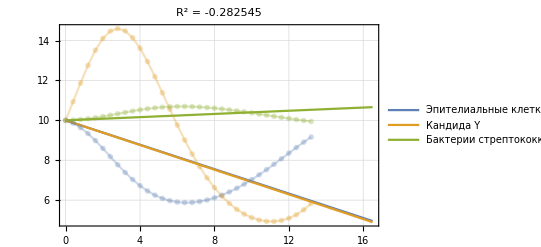

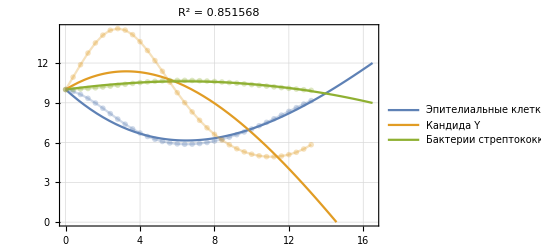

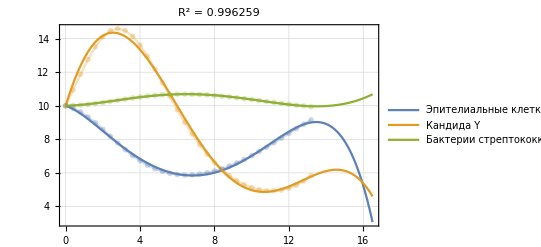

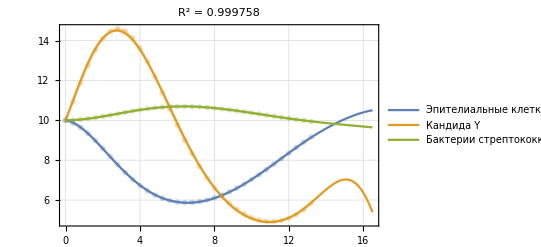

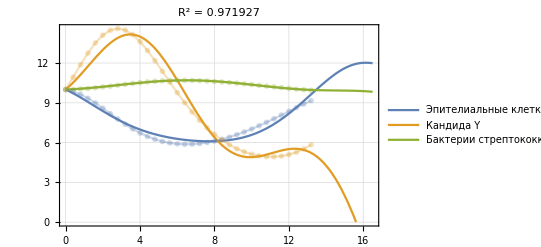

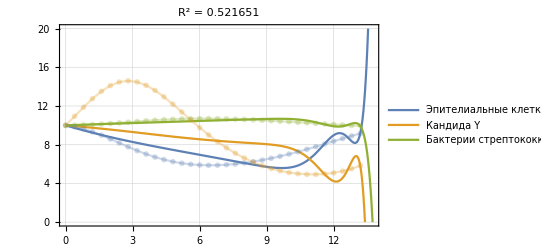

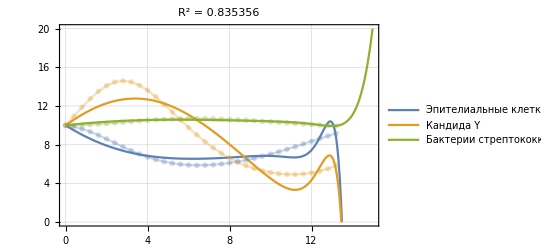

```mathematica
ShowSearch[1]
ShowSearch[2]
ShowSearch[3]
ShowSearch[4]
ShowSearch[4,15]
ShowSearch[6]
ShowSearch[123]
```

#### search step

```mathematica
xs=preData["X"][[1;;;;10]]
ts=preData["t"][[1;;;;10]]
sol = xGen[1,preData["X"]//First]/@%;
error = sol-%%%;
normed=#.#&[Flatten[error]];
minSol=FindMinimum[normed,{Subscript[a, 1],Subscript[A, 1,1],Subscript[A, 2,1],Subscript[A, 3,1],Subscript[a, 2],Subscript[A, 1,2],Subscript[A, 2,2],Subscript[A, 3,2],Subscript[a, 3],Subscript[A, 1,3],Subscript[A, 2,3],Subscript[A, 3,3]}]
solved=With[{$=Simplify[xGen[1,preData["X"]//First][#]/.minSol[[2]]]},$&];
solved
Show[
Plot[Evaluate[solved[t]],{t,preData["t"]//Min,1.25ts//Max},PlotRange->{{0,All},{0,20}},Frame->True,GridLines->Automatic,PlotLegends->{"Эпителиальные клетки X", "Кандида Y","Бактерии стрептококков Z"},PlotStyle->Directive[Thick]],
ListPlot[Transpose[xs],PlotMarkers->{"OpenMarkers"},PlotStyle->Opacity[.3],
DataRange->{0,Last[ts]},Joined->True],
PlotLabel->StringForm["R^2 = ``",Mean[kmCoefficientR2Raw[solved,Transpose@xs,ts]]]
]
```

{{10.,10.,10.},{9.85605,10.9367,10.0152},{9.63268,11.8723,10.0425},{9.33769,12.7517,10.0816},{8.98501,13.5144,10.1316},{8.59313,14.103,10.1907},{8.18291,14.4728,10.2565},{7.7749,14.5993,10.3259},{7.387,14.4815,10.396},{7.03307,14.1401,10.4633},{6.72243,13.6123,10.5252},{6.46026,12.9444,10.5794},{6.24837,12.1845,10.624},{6.0862,11.3774,10.6581},{5.97166,10.5609,10.6811},{5.90187,9.76486,10.6931},{5.87363,9.01072,10.6945},{5.88372,8.31288,10.686},{5.9291,7.67977,10.6683},{6.00698,7.1154,10.6426},{6.11482,6.62064,10.6097},{6.25033,6.19434,10.5706},{6.41138,5.8342,10.5265},{6.59596,5.53747,10.4781},{6.80204,5.30145,10.4263},{7.02757,5.12388,10.3721},{7.27027,5.00316,10.3162},{7.5276,4.93864,10.2594},{7.79657,4.93069,10.2024},{8.07365,4.98087,10.146},{8.35454,5.09198,10.091},{8.63414,5.26811,10.038},{8.90625,5.51455,9.98811},{9.16354,5.83758,9.94204}}

{0.,0.4,0.8,1.2,1.6,2.,2.4,2.8,3.2,3.6,4.,4.4,4.8,5.2,5.6,6.,6.4,6.8,7.2,7.6,8.,8.4,8.8,9.2,9.6,10.,10.4,10.8,11.2,11.6,12.,12.4,12.8,13.2}

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{365.241,{a_1→3776.95,A_(1,1)→-157.263,A_(2,1)→-110.217,A_(3,1)→-110.217,a_2→4523.06,A_(1,2)→304.054,A_(2,2)→-378.181,A_(3,2)→-378.181,a_3→-1384.22,A_(1,3)→132.149,A_(2,3)→3.13675,A_(3,3)→3.13675}}

{10.-0.305893 #1,10.-0.309247 #1,10.+0.0400323 #1}&

-Graphics-

```mathematica
∫_0^t fGen[xGenRules[1,First@preData["X"],minSol[[2]],0][τ]]ⅆτ;
xGen[2,First@preData["X"],minSol[[2]]];
%%-%[t]
```

{-10.,-10.,-10.}

```mathematica
xGen[2]
```

{10.+10. #1 a_1-0.152947 #1^2 a_1+100. #1 A_(1,1)-3.05893 #1^2 A_(1,1)+0.0311902 #1^3 A_(1,1)+100. #1 A_(2,1)-3.0757 #1^2 A_(2,1)+0.0315322 #1^3 A_(2,1)+100. #1 A_(3,1)-1.3293 #1^2 A_(3,1)-0.00408187 #1^3 A_(3,1),10.+10. #1 a_2-0.154624 #1^2 a_2+100. #1 A_(1,2)-3.0757 #1^2 A_(1,2)+0.0315322 #1^3 A_(1,2)+100. #1 A_(2,2)-3.09247 #1^2 A_(2,2)+0.0318779 #1^3 A_(2,2)+100. #1 A_(3,2)-1.34607 #1^2 A_(3,2)-0.00412662 #1^3 A_(3,2),10.+10. #1 a_3+0.0200162 #1^2 a_3+100. #1 A_(1,3)-1.3293 #1^2 A_(1,3)-0.00408187 #1^3 A_(1,3)+100. #1 A_(2,3)-1.34607 #1^2 A_(2,3)-0.00412662 #1^3 A_(2,3)+100. #1 A_(3,3)+0.400323 #1^2 A_(3,3)+0.000534195 #1^3 A_(3,3)}&

```mathematica
step=2
xs=preData["X"][[1;;;;10]];
ts=preData["t"][[1;;;;10]];
sol = xGen[step,preData["X"]//First,minSol[[2]]]/@%;
error = sol-%%%;
normed=#.#&[Flatten[error]];
minSol=FindMinimum[normed,{Subscript[a, 1],Subscript[A, 1,1],Subscript[A, 2,1],Subscript[A, 3,1],Subscript[a, 2],Subscript[A, 1,2],Subscript[A, 2,2],Subscript[A, 3,2],Subscript[a, 3],Subscript[A, 1,3],Subscript[A, 2,3],Subscript[A, 3,3]}]
solved=With[{$=Simplify[xGen[step][#]/.minSol[[2]]]},$&];
solved
Show[
Plot[Evaluate[solved[t]],{t,preData["t"]//Min,1.25ts//Max},PlotRange->{{0,All},{0,20}},Frame->True,GridLines->Automatic,PlotLegends->{"Эпителиальные клетки X", "Кандида Y","Бактерии стрептококков Z"},PlotStyle->Directive[Thick]],
ListPlot[Transpose[xs],PlotMarkers->{"OpenMarkers"},PlotStyle->Opacity[.3],
DataRange->{0,Last[ts]},Joined->True],
PlotLabel->StringForm["R^2 = ``",Mean[kmCoefficientR2Raw[solved,Transpose@xs,ts]]]
]
```

2

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{140.51,{a_1→467.091,A_(1,1)→-232.828,A_(2,1)→225.182,A_(3,1)→-39.0752,a_2→-24850.7,A_(1,2)→38.4932,A_(2,2)→246.778,A_(3,2)→2199.81,a_3→-381.251,A_(1,3)→342.955,A_(2,3)→-335.283,A_(3,3)→30.4554}}

{10.-1.26758 #1+0.117046 #1^2-0.00199153 #1^3,10.+0.871863 #1-0.147186 #1^2+0.00275653 #1^3,10.+0.191984 #1-0.0146917 #1^2-0.0000402352 #1^3}&

-Graphics-

```mathematica
minSol[[2]]
```

{a_1→467.091,A_(1,1)→-232.828,A_(2,1)→225.182,A_(3,1)→-39.0752,a_2→-24850.7,A_(1,2)→38.4932,A_(2,2)→246.778,A_(3,2)→2199.81,a_3→-381.251,A_(1,3)→342.955,A_(2,3)→-335.283,A_(3,3)→30.4554}

```mathematica
∫_0^t fGen[xGenRules[2,First@preData["X"],minSol[[2]],0][τ]]ⅆτ
```

{t ((10.+t (-0.633791+(0.0390152-0.000497884 t) t)) a_1+(100.+t (-12.6758+t (1.31589+t (-0.0841401+t (0.00374971+(-0.0000777001+5.66601×10^-7 t) t))))) A_(1,1)+100. A_(2,1)+100. A_(3,1)+t ((-1.9786+t (-0.468855+t (0.074067+t (-0.00449159+(0.000102628-7.84246×10^-7 t) t)))) A_(2,1)+(-5.37799+t (0.260061+t (0.00519404+t (-0.000410189+(4.09162×10^-6+1.14471×10^-8 t) t)))) A_(3,1))),t ((10.+t (0.435931+(-0.049062+0.000689132 t) t)) a_2+(100.+t (-1.9786+t (-0.468855+t (0.074067+t (-0.00449159+(0.000102628-7.84246×10^-7 t) t))))) A_(1,2)+100. A_(2,2)+100. A_(3,2)+t ((8.71863+t (-0.727859+t (-0.0503804+t (0.00529408+(-0.000135241+1.08549×10^-6 t) t)))) A_(2,2)+(5.31923+t (-0.483798+t (-0.0034759+t (0.00053131+(-5.76268×10^-6-1.58442×10^-8 t) t)))) A_(3,2))),t ((10.+t (0.095992+(-0.00489724-0.0000100588 t) t)) a_3+(100.+t (-5.37799+t (0.260061+t (0.00519404+t (-0.000410189+(4.09162×10^-6+1.14471×10^-8 t) t))))) A_(1,3)+100. A_(2,3)+100. A_(3,3)+t ((5.31923+t (-0.483798+t (-0.0034759+t (0.00053131+(-5.76268×10^-6-1.58442×10^-8 t) t)))) A_(2,3)+(1.91984+t (-0.0856589+t (-0.00161146+t (0.0000400796+(1.97041×10^-7+2.31267×10^-10 t) t)))) A_(3,3)))}

```mathematica
∫_0^t fGen[xGenRules[2,First@preData["X"],minSol[[2]],0][τ]]ⅆτ;
xGen[3,First@preData["X"],minSol[[2]]];
%%-%[t]
```

{-10.,-10.,-10.}

```mathematica
step=3
xs=preData["X"][[1;;;;10]];
ts=preData["t"][[1;;;;10]];
sol = xGen[step,preData["X"]//First,minSol[[2]]]/@%;
error = sol-%%%;
normed=#.#&[Flatten[error]];
minSol=FindMinimum[normed,{Subscript[a, 1],Subscript[A, 1,1],Subscript[A, 2,1],Subscript[A, 3,1],Subscript[a, 2],Subscript[A, 1,2],Subscript[A, 2,2],Subscript[A, 3,2],Subscript[a, 3],Subscript[A, 1,3],Subscript[A, 2,3],Subscript[A, 3,3]}]
solved=With[{$=Simplify[xGen[step][#]/.minSol[[2]]]},$&];
solved
Show[
Plot[Evaluate[solved[t]],{t,preData["t"]//Min,1.25ts//Max},PlotRange->{{0,All},{0,20}},Frame->True,GridLines->Automatic,PlotLegends->{"Эпителиальные клетки X", "Кандида Y","Бактерии стрептококков Z"},PlotStyle->Directive[Thick]],
ListPlot[Transpose[xs],PlotMarkers->{"OpenMarkers"},PlotStyle->Opacity[.3],
DataRange->{0,Last[ts]},Joined->True],
PlotLabel->StringForm["R^2 = ``",Mean[kmCoefficientR2Raw[solved,Transpose@xs,ts]]]
]
```

3

{1.73504,{a_1→-20.8159,A_(1,1)→0.288343,A_(2,1)→-0.0694891,A_(3,1)→1.85899,a_2→-3.50651,A_(1,2)→0.174442,A_(2,2)→-0.00617077,A_(3,2)→0.218313,a_3→3.00749,A_(1,3)→-0.04177,A_(2,3)→0.00981778,A_(3,3)→-0.268477}}

{10.-0.374464 #1-0.322206 #1^2+0.083324 #1^3-0.00938855 #1^4+0.000630783 #1^5-0.0000219295 #1^6+2.39152×10^-7 #1^7,10.+3.59333 #1-0.76629 #1^2-0.0108794 #1^3+0.010056 #1^4-0.000700198 #1^5+0.000017479 #1^6-1.46963×10^-7 #1^7,10.+0.0320307 #1+0.0501247 #1^2-0.00734356 #1^3+0.000151308 #1^4+0.0000115894 #1^5-2.80385×10^-7 #1^6-6.9579×10^-10 #1^7}&

-Graphics-

4

{19.2629,{a_1→-3.53811,A_(1,1)→0.126773,A_(2,1)→-0.00914231,A_(3,1)→0.233813,a_2→-6.03512,A_(1,2)→-0.00417034,A_(2,2)→0.0207535,A_(3,2)→0.594291,a_3→-1.80872,A_(1,3)→0.0173191,A_(2,3)→0.00362717,A_(3,3)→0.160604}}

{10.-0.236662 #1-0.301909 #1^2+0.0179812 #1^3+0.0121529 #1^4-0.00210819 #1^5+0.0000333208 #1^6+0.0000325502 #1^7-5.81385×10^-6 #1^8+5.71375×10^-7 #1^9-3.7274×10^-8 #1^10+1.65589×10^-9 #1^11-4.8856×10^-11 #1^12+9.01131×10^-13 #1^13-9.25137×10^-15 #1^14+3.98764×10^-17 #1^15,10.+0.73624 #1+0.401763 #1^2+0.00562082 #1^3-0.0344425 #1^4+0.000330649 #1^5+0.00116469 #1^6-0.000131536 #1^7-1.30101×10^-6 #1^8+1.27283×10^-6 #1^9-1.14542×10^-7 #1^10+5.3006×10^-9 #1^11-1.45487×10^-10 #1^12+2.39198×10^-12 #1^13-2.1841×10^-14 #1^14+8.5419×10^-17 #1^15,10.+0.0677336 #1+0.0272883 #1^2-0.00290705 #1^3-0.000113707 #1^4+4.37912×10^-6 #1^5+2.27244×10^-7 #1^6+9.52068×10^-8 #1^7-5.70339×10^-9 #1^8-1.64497×10^-10 #1^9+1.64844×10^-11 #1^10-1.57153×10^-13 #1^11-1.09708×10^-14 #1^12+2.48161×10^-16 #1^13-8.56694×10^-19 #1^14-3.02876×10^-21 #1^15}&

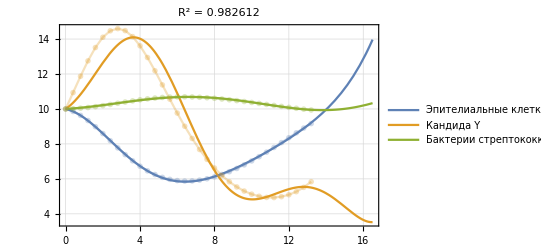

```mathematica
step=4
xs=preData["X"][[1;;;;10]];
ts=preData["t"][[1;;;;10]];
sol = xGen[step,preData["X"]//First,minSol[[2]]]/@%;
error = sol-%%%;
normed=#.#&[Flatten[error]];
minSol=FindMinimum[normed,{Subscript[a, 1],Subscript[A, 1,1],Subscript[A, 2,1],Subscript[A, 3,1],Subscript[a, 2],Subscript[A, 1,2],Subscript[A, 2,2],Subscript[A, 3,2],Subscript[a, 3],Subscript[A, 1,3],Subscript[A, 2,3],Subscript[A, 3,3]}]
solved=With[{$=Simplify[xGen[step][#]/.minSol[[2]]]},$&];
solved
Show[
Plot[Evaluate[solved[t]],{t,preData["t"]//Min,1.25ts//Max},PlotRange->{{0,All},{0,20}},Frame->True,GridLines->Automatic,PlotLegends->{"Эпителиальные клетки X", "Кандида Y","Бактерии стрептококков Z"},PlotStyle->Directive[Thick]],
ListPlot[Transpose[xs],PlotMarkers->{"OpenMarkers"},PlotStyle->Opacity[.3],
DataRange->{0,Last[ts]},Joined->True],
PlotLabel->StringForm["R^2 = ``",Mean[kmCoefficientR2Raw[solved,Transpose@xs,ts]]]
]
```

#### built-in

```mathematica
NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.SearchParams[6]["A"]),{x1[0],x2[0],x3[0]}==First[preData["X"]]},{x1[t],x2[t],x3[t]},{t,preData["t"]//Min,1.25preData["t"]//Max}];
Nsolution=With[{$=Through[First[%[[All,All,2,0]]][#]]},$&]
```

{InterpolatingFunction[…][#1],InterpolatingFunction[…][#1],InterpolatingFunction[…][#1]}&

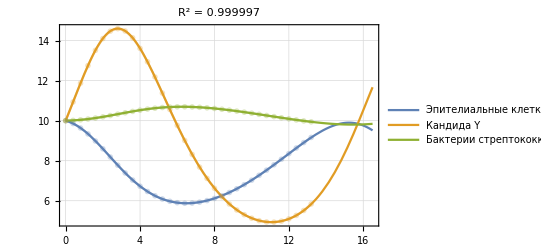

```mathematica
Show[
Plot[Evaluate[Nsolution[t]],{t,preData["t"]//Min,1.25preData["t"]//Max},PlotRange->{{0,All},{0,20}},Frame->True,GridLines->Automatic,PlotLegends->{"Эпителиальные клетки X", "Кандида Y","Бактерии стрептококков Z"},PlotStyle->Directive[Thick]],
ListPlot[Transpose[xs],PlotMarkers->{"OpenMarkers"},PlotStyle->Opacity[.3],
DataRange->{0,Last[preData["t"]]},Joined->True],
PlotLabel->StringForm["R^2 = ``",Mean[kmCoefficientR2Raw[Nsolution,Transpose@preData["X"],preData["t"]]]]
]
```

```mathematica
NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.SearchParams[6]["A"]),{x1[0],x2[0],x3[0]}==First[preData["X"]]},{x1[t],x2[t],x3[t]},{t,1. 10^7,1. 10^7}];
NsolutionInfty=With[{$=Through[First[%[[All,All,2,0]]][#]]},$&];
NsolutionInfty[1. 10^7]
```

{-193.215,5.53862×10^-75,1.00487×10^-43}

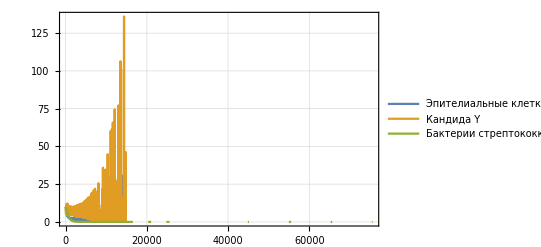

```mathematica
NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.(SearchParams[6]["A"])),{x1[0],x2[0],x3[0]}==First[preData["X"]]},{x1[t],x2[t],x3[t]},{t,0.,1. 10^5}];
NsolutionInfty=With[{$=Through[First[%[[All,All,2,0]]][#]]},$&];
Plot[Evaluate[NsolutionInfty[t]],{t,0,1. 10^5},PlotRange->{{0,All},{0,All}},Frame->True,GridLines->Automatic,PlotStyle->Directive[Thick],PlotLegends->{"Эпителиальные клетки X", "Кандида Y","Бактерии стрептококков Z"}]
```

```mathematica
Solve[{1,x1,x2,x3}.SearchParams[#]["A"]=={0,0,0}]&/@Range[7]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-110.217,-110.217,-157.263,3776.95},{-378.181,-378.181,304.054,4523.06},{3.13675,3.13675,132.149,-1384.22}} may contain significant numerical errors.

{{{x1→9.99995,x2→-2.62838×10^10,x3→2.62838×10^10}},{{x1→8.47431,x2→8.45768,x3→10.1997}},{{x1→7.53551,x2→1.31896,x3→10.0779}},{{x1→8.19617,x2→4.86741,x3→9.17032}},{{x1→2.54964,x2→-0.98987,x3→1.89336}},{{x1→15.5526,x2→11.4473,x3→22.2778}},{{x1→1.69525×10^7,x2→2.95577×10^8,x3→-368.816}}}

#### built-in 2

```mathematica
NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.SearchParamsCyclic[5,5]["A"]),{x1[0],x2[0],x3[0]}==First[preData["X"]]},{x1[t],x2[t],x3[t]},{t,preData["t"]//Min,1.25preData["t"]//Max}];
Nsolution=With[{$=Through[First[%[[All,All,2,0]]][#]]},$&]
```

{InterpolatingFunction[…][#1],InterpolatingFunction[…][#1],InterpolatingFunction[…][#1]}&

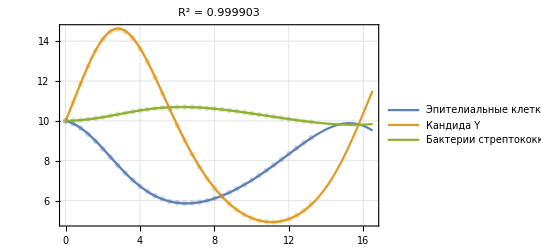

```mathematica
Show[
Plot[Evaluate[Nsolution[t]],{t,preData["t"]//Min,1.25preData["t"]//Max},PlotRange->{{0,All},{0,20}},Frame->True,GridLines->Automatic,PlotLegends->{"Эпителиальные клетки X", "Кандида Y","Бактерии стрептококков Z"},PlotStyle->Directive[Thick]],
ListPlot[Transpose[xs],PlotMarkers->{"OpenMarkers"},PlotStyle->Opacity[.3],
DataRange->{0,Last[preData["t"]]},Joined->True],
PlotLabel->StringForm["R^2 = ``",Mean[kmCoefficientR2Raw[Nsolution,Transpose@preData["X"],preData["t"]]]]
]
```

```mathematica
NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.SearchParams[6]["A"]),
{x1[0],x2[0],x3[0]}==First[preData["X"]]},{x1[t],x2[t],x3[t]},{t,1. 10^7,1. 10^7}];
NsolutionInfty=With[{$=Through[First[%[[All,All,2,0]]][#]]},$&];
NsolutionInfty[1. 10^7]
```

{-2300.49,-1.14715×10^-113,414.434}

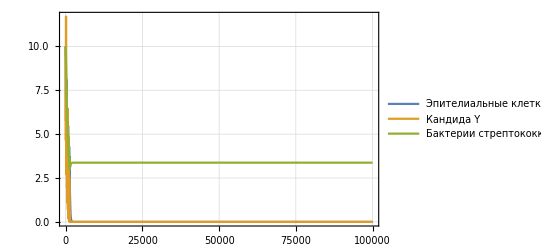

```mathematica
NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.(SearchParamsCyclic[5,50]["A"])),
WhenEvent[x1[t]<0,x1[t]->0.001],WhenEvent[x2[t]<0,x2[t]->0.001],WhenEvent[x3[t]<0,x3[t]->0.001],
{x1[0],x2[0],x3[0]}==First[preData["X"]]},{x1[t],x2[t],x3[t]},{t,0.,1. 10^5}];
NsolutionInfty=With[{$=Through[First[%[[All,All,2,0]]][#]]},$&];
Plot[Evaluate[NsolutionInfty[t]],{t,0,1. 10^5},PlotRange->{{0,All},{0,All}},Frame->True,GridLines->Automatic,PlotStyle->Directive[Thick],PlotLegends->{"Эпителиальные клетки X", "Кандида Y","Бактерии стрептококков Z"}]
```

```mathematica
Solve[{1,x1,x2,x3}.SearchParams[#]["A"]=={0,0,0}]&/@Range[7]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-110.217,-110.217,-157.263,3776.95},{-378.181,-378.181,304.054,4523.06},{3.13675,3.13675,132.149,-1384.22}} may contain significant numerical errors.

{{{x1→9.99995,x2→-2.62838×10^10,x3→2.62838×10^10}},{{x1→8.47431,x2→8.45768,x3→10.1997}},{{x1→7.53551,x2→1.31896,x3→10.0779}},{{x1→8.19617,x2→4.86741,x3→9.17032}},{{x1→2.54964,x2→-0.98987,x3→1.89336}},{{x1→15.5526,x2→11.4473,x3→22.2778}},{{x1→1.69525×10^7,x2→2.95577×10^8,x3→-368.816}}}

```mathematica
ClearAll[x1,x2,x3,t]
```

```mathematica
NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.SearchParamsCyclic[5,5]["A"]),
WhenEvent[x1[t]<0,x1[t]->0.001],WhenEvent[x2[t]<0,x2[t]->0.001],WhenEvent[x3[t]<0,x3[t]->0.001],
{x1[0],x2[0],x3[0]}==First[preData["X"]]},{x1[t],x2[t],x3[t]},{t,1. 10^4,1. 10^4}];
NsolutionInfty=With[{$=Through[First[%[[All,All,2,0]]][#]]},$&];
NsolutionInfty[1. 10^4]
```

{1.02423×10^-21,3.15393×10^-10,3.37454}

#### system

```mathematica
SearchParams[50]["A"]//Transpose
```

{{-0.0364527,2.94494×10^-6,-0.00199897,0.000515721},{-2.366,0.00844258,0.0608227,0.168655},{-0.288748,0.00009439,0.0107453,0.0195818}}

```mathematica
points
```

{{10.,10.,10.},32,{10.+1.79274×10^11 A_(1,1)+102+9.65984 (1. a_1+3.0312 A_(1,1)+7.49537 A_(2,1)+10.539 A_(3,1))+13.2 (10. a_1+100. A_(1,1)+100. A_(2,1)+100. A_(3,1)),10.+103+19 1,104+13.2 (1)}}
 |  |  |  |

```mathematica
LeastSquares[Transpose[Chop@Rest[Simplify@points-10]][[1]]/.{Plus->List},Transpose[Rest[xs]-10][[1]]]
```

{-0.0364527/a_1,(2.94496×10^-6)/(A_(1,1)),-0.00199899/(A_(2,1)),0.000515725/(A_(3,1))}

```mathematica
Length[#]&/@(Transpose[Rest[points-10]][[1]]/.{Plus->List})
```

{101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101}

### steps

```mathematica
preData["X"][[1;;;;20]]
preData["t"][[1;;;;20]]
sol = xGen[2,preData["X"]//First]/@%;
error = sol-%%%;
```

{{10.,10.,10.},{9.63268,11.8723,10.0425},{8.98501,13.5144,10.1316},{8.18291,14.4728,10.2565},{7.387,14.4815,10.396},{6.72243,13.6123,10.5252},{6.24837,12.1845,10.624},{5.97166,10.5609,10.6811},{5.87363,9.01072,10.6945},{5.9291,7.67977,10.6683},{6.11482,6.62064,10.6097},{6.41138,5.8342,10.5265},{6.80204,5.30145,10.4263},{7.27027,5.00316,10.3162},{7.79657,4.93069,10.2024},{8.35454,5.09198,10.091},{8.90625,5.51455,9.98811}}

{0.,0.8,1.6,2.4,3.2,4.,4.8,5.6,6.4,7.2,8.,8.8,9.6,10.4,11.2,12.,12.8}

```mathematica
normed=#.#&/@[Transpose[error]];
```

```mathematica
minSol1=FindMinimum[normed[1],{Subscript[a, 1],Subscript[A, 1,1],Subscript[A, 2,1],Subscript[A, 3,1],Subscript[a, 2],Subscript[A, 1,2],Subscript[A, 2,2],Subscript[A, 3,2],Subscript[a, 3],Subscript[A, 1,3],Subscript[A, 2,3],Subscript[A, 3,3]}]
```

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{178.397,{a_1→31.4558,A_(1,1)→63.1189,A_(2,1)→55.6576,A_(3,1)→-121.923,a_2→60.2946,A_(1,2)→-576.835,A_(2,2)→409.28,A_(3,2)→161.525,a_3→14.8817,A_(1,3)→113.691,A_(2,3)→-11.9602,A_(3,3)→-103.22}}

```mathematica
solved=With[{$=Simplify[xGen[2,preData["X"]//First][#]/.minSol[[2]]]},$&];
```

```mathematica
solved
```

{10.-0.0529337 #1-0.0211364 #1^2+0.0000747442 #1^3,10.-0.0540761 #1-0.0314813 #1^2+0.00012207 #1^3,10.-0.0520544 #1+0.00864353 #1^2-0.0000267029 #1^3}&

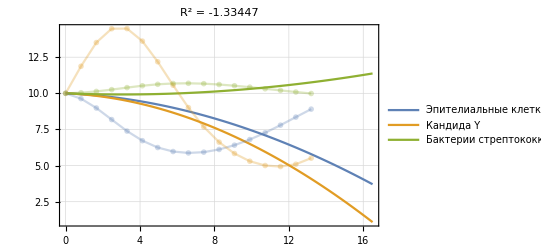

```mathematica
Show[
Plot[Evaluate[solved[t]],{t,preData["t"]//Min,1.25preData["t"]//Max},PlotRange->{{0,All},{0,20}},Frame->True,GridLines->Automatic,PlotLegends->{"Эпителиальные клетки X", "Кандида Y","Бактерии стрептококков Z"},PlotStyle->Directive[Thick]],
ListPlot[Transpose[preData["X"][[1;;;;20]]],PlotMarkers->{"OpenMarkers"},PlotStyle->Opacity[.3],
DataRange->{0,Last[preData["t"]]},Joined->True],
PlotLabel->StringForm["R^2 = ``",Mean[kmCoefficientR2Raw[solved,Transpose@preData["X"],preData["t"]]]]
]
```

# MicrobiotaExperiment 2021

## Task

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danila/Documents/Thesis

```mathematica
dataRaw=First@Import["./data/MicrobiotaExperiment 2021.xlsx"];
```

### preData

```mathematica
dataRaw[[{1,2,4,3,5}]];
preData=<|"title"->%[[1,1]],"names"->%[[3;;,1]],"X"->Transpose[%[[3;;,2;;]]],"t"->#,"N"->Length[#]|>&[%[[2,2;;]]]
```

<|title→Эксперимент по кокультивированию клеток с конкурентными микроорганизмами,names→{Эпителиальные клетки,Патологический микрорганизм,Антагонистичный (противопатологический организм)},X→{{10.,10.,10.},{9.98927,10.0924,10.001},{9.97773,10.1851,10.0021},{9.96537,10.2783,10.0033},{9.95219,10.3717,10.0046},{9.9382,10.4655,10.0061},{9.92339,10.5594,10.0077},{9.90777,10.6536,10.0094},{9.89134,10.7479,10.0112},{9.8741,10.8423,10.0131},{9.85605,10.9367,10.0152},{9.8372,11.0312,10.0174},{9.81756,11.1256,10.0197},{9.79712,11.2198,10.0221},{9.77591,11.314,10.0246},{9.75393,11.4079,10.0273},{9.73118,11.5015,10.0301},{9.70767,11.5948,10.033},{9.68341,11.6878,10.036},{9.65841,11.7803,10.0392},{9.63268,11.8723,10.0425},{9.60622,11.9638,10.0459},{9.57906,12.0546,10.0494},{9.55118,12.1448,10.053},{9.52262,12.2342,10.0567},{9.49339,12.3228,10.0606},{9.4635,12.4105,10.0646},{9.43297,12.4973,10.0687},{9.40182,12.5832,10.0729},{9.37005,12.668,10.0772},{9.33769,12.7517,10.0816},{9.30475,12.8342,10.0861},{9.27125,12.9155,10.0908},{9.2372,12.9955,10.0955},{9.20261,13.0742,10.1004},{9.16751,13.1514,10.1053},{9.13192,13.2272,10.1104},{9.09585,13.3014,10.1155},{9.05933,13.3741,10.1208},{9.02237,13.4451,10.1261},{8.98501,13.5144,10.1316},{8.94725,13.582,10.1371},{8.90913,13.6477,10.1427},{8.87065,13.7116,10.1485},{8.83184,13.7736,10.1542},{8.79271,13.8337,10.1601},{8.75328,13.8917,10.1661},{8.71359,13.9477,10.1721},{8.67365,14.0016,10.1782},{8.63349,14.0534,10.1844},{8.59313,14.103,10.1907},{8.55258,14.1504,10.197},{8.51187,14.1956,10.2034},{8.47103,14.2385,10.2098},{8.43007,14.2791,10.2163},{8.389,14.3173,10.2229},{8.34786,14.3532,10.2295},{8.30666,14.3868,10.2362},{8.26542,14.4179,10.2429},{8.22416,14.4466,10.2497},{8.18291,14.4728,10.2565},{8.14169,14.4966,10.2633},{8.10051,14.518,10.2702},{8.0594,14.5368,10.2771},{8.01837,14.5532,10.284},{7.97743,14.5671,10.2909},{7.93662,14.5785,10.2979},{7.89594,14.5874,10.3049},{7.85542,14.5939,10.3119},{7.81506,14.5978,10.3189},{7.7749,14.5993,10.3259},{7.73494,14.5984,10.333},{7.6952,14.5949,10.34},{7.6557,14.5891,10.347},{7.61645,14.5808,10.3541},{7.57746,14.5701,10.3611},{7.53876,14.557,10.3681},{7.50035,14.5416,10.3751},{7.46224,14.5239,10.3821},{7.42446,14.5038,10.389},{7.387,14.4815,10.396},{7.34989,14.4569,10.4029},{7.31313,14.4301,10.4097},{7.27674,14.4011,10.4166},{7.24073,14.3699,10.4234},{7.2051,14.3367,10.4302},{7.16987,14.3013,10.4369},{7.13504,14.264,10.4436},{7.10063,14.2246,10.4502},{7.06663,14.1833,10.4568},{7.03307,14.1401,10.4633},{6.99994,14.095,10.4698},{6.96725,14.048,10.4762},{6.93502,13.9993,10.4826},{6.90324,13.9488,10.4889},{6.87192,13.8967,10.4951},{6.84107,13.8429,10.5013},{6.8107,13.7875,10.5074},{6.78079,13.7306,10.5134},{6.75137,13.6722,10.5194},{6.72243,13.6123,10.5252},{6.69398,13.551,10.531},{6.66602,13.4884,10.5367},{6.63855,13.4244,10.5424},{6.61158,13.3592,10.5479},{6.5851,13.2928,10.5534},{6.55913,13.2253,10.5588},{6.53366,13.1566,10.5641},{6.50869,13.0869,10.5692},{6.48422,13.0161,10.5743},{6.46026,12.9444,10.5794},{6.4368,12.8718,10.5843},{6.41385,12.7983,10.5891},{6.3914,12.7239,10.5938},{6.36946,12.6488,10.5984},{6.34802,12.573,10.6029},{6.32709,12.4965,10.6074},{6.30666,12.4194,10.6117},{6.28673,12.3416,10.6159},{6.2673,12.2633,10.62},{6.24837,12.1845,10.624},{6.22994,12.1052,10.6279},{6.21201,12.0255,10.6317},{6.19457,11.9454,10.6354},{6.17763,11.865,10.6389},{6.16117,11.7843,10.6424},{6.14521,11.7033,10.6457},{6.12973,11.6221,10.649},{6.11474,11.5407,10.6521},{6.10023,11.4591,10.6551},{6.0862,11.3774,10.6581},{6.07264,11.2956,10.6609},{6.05956,11.2138,10.6636},{6.04695,11.1319,10.6661},{6.03481,11.0501,10.6686},{6.02314,10.9683,10.671},{6.01193,10.8865,10.6732},{6.00118,10.8049,10.6754},{5.99089,10.7234,10.6774},{5.98105,10.6421,10.6793},{5.97166,10.5609,10.6811},{5.96272,10.48,10.6828},{5.95422,10.3993,10.6844},{5.94617,10.3188,10.6859},{5.93855,10.2387,10.6872},{5.93137,10.1588,10.6885},{5.92462,10.0793,10.6896},{5.9183,10.0001,10.6907},{5.9124,9.92129,10.6916},{5.90693,9.84287,10.6924},{5.90187,9.76486,10.6931},{5.89723,9.68727,10.6937},{5.893,9.61012,10.6942},{5.88918,9.53343,10.6946},{5.88577,9.45722,10.6949},{5.88276,9.3815,10.6951},{5.88015,9.30628,10.6952},{5.87794,9.23158,10.6952},{5.87611,9.15741,10.6951},{5.87468,9.08379,10.6949},{5.87363,9.01072,10.6945},{5.87296,8.93823,10.6941},{5.87268,8.86631,10.6936},{5.87277,8.79498,10.693},{5.87323,8.72424,10.6923},{5.87407,8.65411,10.6915},{5.87528,8.5846,10.6905},{5.87685,8.51572,10.6895},{5.87878,8.44746,10.6885},{5.88107,8.37985,10.6873},{5.88372,8.31288,10.686},{5.88672,8.24656,10.6846},{5.89007,8.18089,10.6832},{5.89376,8.11589,10.6816},{5.8978,8.05155,10.68},{5.90217,7.98789,10.6782},{5.90689,7.9249,10.6764},{5.91194,7.86259,10.6745},{5.91733,7.80096,10.6726},{5.92305,7.74002,10.6705},{5.9291,7.67977,10.6683},{5.93547,7.6202,10.6661},{5.94216,7.56133,10.6638},{5.94917,7.50315,10.6614},{5.9565,7.44566,10.659},{5.96414,7.38888,10.6564},{5.97209,7.33278,10.6538},{5.98035,7.27739,10.6511},{5.98892,7.22269,10.6483},{5.9978,7.16869,10.6455},{6.00698,7.1154,10.6426},{6.01645,7.0628,10.6396},{6.02623,7.0109,10.6365},{6.0363,6.95969,10.6334},{6.04666,6.90918,10.6302},{6.0573,6.85936,10.627},{6.06824,6.81023,10.6236},{6.07946,6.7618,10.6202},{6.09097,6.71406,10.6168},{6.10275,6.667,10.6133},{6.11482,6.62064,10.6097},{6.12716,6.57496,10.606},{6.13978,6.52997,10.6023},{6.15268,6.48566,10.5986},{6.16583,6.44202,10.5947},{6.17926,6.39906,10.5909},{6.19295,6.35678,10.5869},{6.20691,6.31517,10.5829},{6.22112,6.27422,10.5789},{6.2356,6.23395,10.5748},{6.25033,6.19434,10.5706},{6.26532,6.15539,10.5664},{6.28057,6.1171,10.5622},{6.29606,6.07947,10.5579},{6.31181,6.0425,10.5535},{6.3278,6.00617,10.5491},{6.34404,5.97049,10.5447},{6.36051,5.93546,10.5402},{6.37723,5.90107,10.5357},{6.39419,5.86731,10.5311},{6.41138,5.8342,10.5265},{6.42882,5.80172,10.5218},{6.44648,5.76987,10.5171},{6.46438,5.73865,10.5123},{6.4825,5.70806,10.5076},{6.50086,5.67809,10.5027},{6.51944,5.64873,10.4979},{6.53824,5.62,10.493},{6.55726,5.59188,10.488},{6.5765,5.56437,10.4831},{6.59596,5.53747,10.4781},{6.61563,5.51118,10.473},{6.63551,5.48549,10.468},{6.65561,5.4604,10.4629},{6.67592,5.43591,10.4577},{6.69644,5.41203,10.4526},{6.71716,5.38873,10.4474},{6.73808,5.36603,10.4421},{6.75921,5.34392,10.4369},{6.78053,5.32239,10.4316},{6.80204,5.30145,10.4263},{6.82376,5.2811,10.421},{6.84566,5.26132,10.4157},{6.86776,5.24213,10.4103},{6.89004,5.22351,10.4049},{6.91251,5.20547,10.3995},{6.93516,5.18801,10.394},{6.958,5.17112,10.3886},{6.98101,5.1548,10.3831},{7.0042,5.13906,10.3776},{7.02757,5.12388,10.3721},{7.05111,5.10926,10.3666},{7.07481,5.09522,10.361},{7.09868,5.08174,10.3555},{7.12272,5.06882,10.3499},{7.14692,5.05647,10.3443},{7.17128,5.04469,10.3387},{7.1958,5.03346,10.3331},{7.22047,5.0228,10.3275},{7.2453,5.0127,10.3218},{7.27027,5.00316,10.3162},{7.29539,4.99419,10.3105},{7.32066,4.98577,10.3049},{7.34606,4.97791,10.2992},{7.3716,4.97062,10.2935},{7.39728,4.96388,10.2879},{7.42309,4.95771,10.2822},{7.44903,4.95209,10.2765},{7.4751,4.94705,10.2708},{7.50129,4.94256,10.2651},{7.5276,4.93864,10.2594},{7.55403,4.93528,10.2537},{7.58057,4.93249,10.248},{7.60722,4.93027,10.2423},{7.63398,4.92862,10.2366},{7.66084,4.92753,10.2309},{7.6878,4.92701,10.2252},{7.71486,4.92707,10.2195},{7.74201,4.9277,10.2138},{7.76925,4.92891,10.2081},{7.79657,4.93069,10.2024},{7.82398,4.93306,10.1967},{7.85147,4.936,10.191},{7.87902,4.93954,10.1854},{7.90665,4.94366,10.1797},{7.93434,4.94837,10.1741},{7.9621,4.95367,10.1684},{7.98991,4.95957,10.1628},{8.01778,4.96607,10.1572},{8.04569,4.97317,10.1516},{8.07365,4.98087,10.146},{8.10164,4.98919,10.1404},{8.12967,4.99811,10.1349},{8.15773,5.00765,10.1293},{8.18582,5.0178,10.1238},{8.21392,5.02858,10.1183},{8.24203,5.03999,10.1128},{8.27016,5.05203,10.1073},{8.29829,5.06471,10.1018},{8.32642,5.07802,10.0964},{8.35454,5.09198,10.091},{8.38265,5.10659,10.0856},{8.41075,5.12186,10.0802},{8.43882,5.13778,10.0748},{8.46686,5.15437,10.0695},{8.49487,5.17162,10.0642},{8.52283,5.18955,10.0589},{8.55075,5.20816,10.0536},{8.57861,5.22745,10.0484},{8.60641,5.24743,10.0432},{8.63414,5.26811,10.038},{8.66179,5.28949,10.0329},{8.68936,5.31158,10.0278},{8.71685,5.33438,10.0227},{8.74424,5.35791,10.0177},{8.77154,5.38216,10.0127},{8.79873,5.40715,10.0077},{8.8258,5.43288,10.0027},{8.85275,5.45935,9.99782},{8.87957,5.48657,9.99295},{8.90625,5.51455,9.98811},{8.93278,5.5433,9.98331},{8.95916,5.57282,9.97856},{8.98537,5.60311,9.97384},{9.0114,5.63419,9.96917},{9.03726,5.66607,9.96453},{9.06292,5.69874,9.95995},{9.08838,5.73222,9.9554},{9.11365,5.76652,9.9509},{9.13871,5.80163,9.94645},{9.16354,5.83758,9.94204}},t→{0.,0.04,0.08,0.12,0.16,0.2,0.24,0.28,0.32,0.36,0.4,0.44,0.48,0.52,0.56,0.6,0.64,0.68,0.72,0.76,0.8,0.84,0.88,0.92,0.96,1.,1.04,1.08,1.12,1.16,1.2,1.24,1.28,1.32,1.36,1.4,1.44,1.48,1.52,1.56,1.6,1.64,1.68,1.72,1.76,1.8,1.84,1.88,1.92,1.96,2.,2.04,2.08,2.12,2.16,2.2,2.24,2.28,2.32,2.36,2.4,2.44,2.48,2.52,2.56,2.6,2.64,2.68,2.72,2.76,2.8,2.84,2.88,2.92,2.96,3.,3.04,3.08,3.12,3.16,3.2,3.24,3.28,3.32,3.36,3.4,3.44,3.48,3.52,3.56,3.6,3.64,3.68,3.72,3.76,3.8,3.84,3.88,3.92,3.96,4.,4.04,4.08,4.12,4.16,4.2,4.24,4.28,4.32,4.36,4.4,4.44,4.48,4.52,4.56,4.6,4.64,4.68,4.72,4.76,4.8,4.84,4.88,4.92,4.96,5.,5.04,5.08,5.12,5.16,5.2,5.24,5.28,5.32,5.36,5.4,5.44,5.48,5.52,5.56,5.6,5.64,5.68,5.72,5.76,5.8,5.84,5.88,5.92,5.96,6.,6.04,6.08,6.12,6.16,6.2,6.24,6.28,6.32,6.36,6.4,6.44,6.48,6.52,6.56,6.6,6.64,6.68,6.72,6.76,6.8,6.84,6.88,6.92,6.96,7.,7.04,7.08,7.12,7.16,7.2,7.24,7.28,7.32,7.36,7.4,7.44,7.48,7.52,7.56,7.6,7.64,7.68,7.72,7.76,7.8,7.84,7.88,7.92,7.96,8.,8.04,8.08,8.12,8.16,8.2,8.24,8.28,8.32,8.36,8.4,8.44,8.48,8.52,8.56,8.6,8.64,8.68,8.72,8.76,8.8,8.84,8.88,8.92,8.96,9.,9.04,9.08,9.12,9.16,9.2,9.24,9.28,9.32,9.36,9.4,9.44,9.48,9.52,9.56,9.6,9.64,9.68,9.72,9.76,9.8,9.84,9.88,9.92,9.96,10.,10.04,10.08,10.12,10.16,10.2,10.24,10.28,10.32,10.36,10.4,10.44,10.48,10.52,10.56,10.6,10.64,10.68,10.72,10.76,10.8,10.84,10.88,10.92,10.96,11.,11.04,11.08,11.12,11.16,11.2,11.24,11.28,11.32,11.36,11.4,11.44,11.48,11.52,11.56,11.6,11.64,11.68,11.72,11.76,11.8,11.84,11.88,11.92,11.96,12.,12.04,12.08,12.12,12.16,12.2,12.24,12.28,12.32,12.36,12.4,12.44,12.48,12.52,12.56,12.6,12.64,12.68,12.72,12.76,12.8,12.84,12.88,12.92,12.96,13.,13.04,13.08,13.12,13.16,13.2},N→331|>

## Model

{(ⅆ x_1)/ⅆt=x_1(b_1+∑_(i=1)^3 A_(i,1)x_i)
(ⅆ x_2)/ⅆt=x_2(b_2+∑_(i=1)^3 A_(i,2)x_i)
(ⅆ x_3)/ⅆt=x_3(b_3+∑_(i=1)^3 A_(i,3)x_i)

{ⅆLn[x_1]/ⅆt=b_1+∑_(i=1)^3 A_(i,1)x_i
ⅆLn[x_2]/ⅆt=b_2+∑_(i=1)^3 A_(i,2)x_i
ⅆLn[x_3]/ⅆt=b_3+∑_(i=1)^3 A_(i,3)x_i

## Метод Трапеции

## Замена

Применим метод Трапеции

{(Ln[x_1^(k+1)]-Ln[x_1^(k)])/Δt=b_1+∑_(i=1)^3 A_(i,1)(x_i^(k+1)+x_i^(k))/2
(Ln[x_2^(k+1)]-Ln[x_2^(k)])/Δt=b_2+∑_(i=1)^3 A_(i,2)(x_i^(k+1)+x_i^(k))/2
(Ln[x_3^(k+1)]-Ln[x_3^(k)])/Δt=b_3+∑_(i=1)^3 A_(i,3)(x_i^(k+1)+x_i^(k))/2, k=OverBar[1,N-1]

N – количество доступных наблюдений

Определим матрицы X,Y,A:

X_k=[1,(x_1^(k+1)+x_1^(k))/2,(x_2^(k+1)+x_2^(k))/2,(x_3^(k+1)+x_3^(k))/2]– k-ая строка матрицы X

Y_k=[(Ln[x_1^(k+1)]-Ln[x_1^(k)])/Δt,(Ln[x_2^(k+1)]-Ln[x_2^(k)])/Δt,(Ln[x_3^(k+1)]-Ln[x_3^(k)])/Δt]– k-ая строка матрицы Y

k=OverBar[1,N-1]

A=(b_1 | b_2 | b_3
A_(1,1) | A_(1,2) | A_(1,3)
A_(2,1) | A_(2,2) | A_(2,3)
A_(3,1) | A_(3,2) | A_(3,3))

Тогда система примет вид

Y=X.A

## Подготовка данных

### data

```mathematica
data=Join[preData,
<|"X"->(Most[#]+Rest[#])/2&[Join[Transpose@{ConstantArray[1,preData["N"]]},preData["X"],2]],
"Δt"->Differences[preData["t"]],
"Y"->Differences[Map[Log,preData["X"],{2}]]/Differences[preData["t"]]
|>];
```

## Подходы

### Обычный подход

```mathematica
data["X"];
data["Y"];
N@Inverse[Transpose[%%].%%].Transpose[%%].%//MatrixForm
```

(0.198129 | -0.0559291 | -0.0296899
9.16134×10^-7 | 0.0938074 | -1.30876×10^-7
-0.0224005 | -3.81238×10^-7 | 0.00320008
6.65294×10^-6 | -0.0651732 | -9.5042×10^-7)

```mathematica
N@LeastSquares[data["X"],data["Y"]]//MatrixForm
```

(0.198129 | -0.0559291 | -0.0296899
9.16134×10^-7 | 0.0938074 | -1.30876×10^-7
-0.0224005 | -3.81238×10^-7 | 0.00320008
6.65294×10^-6 | -0.0651732 | -9.50421×10^-7)

### Principle Components Regression (PCR)

```mathematica
PCR[data["X"],data["Y"],#]&/@Range[4];
Grid[Join[{{"A","||δy||"}},{MatrixForm[#],MatrixForm[Norm[data["Y"]-data["X"].#]/Norm[data["Y"]]]}&/@%],Frame->All]
```

A | ||δy||
(-0.0000709589 | -0.000135808 | 4.74712×10^-6
-0.000527143 | -0.0010089 | 0.0000352657
-0.000685649 | -0.00131226 | 0.0000458697
-0.000735862 | -0.00140837 | 0.0000492289) | 0.972738
(0.00127315 | -0.000254166 | -0.000190568
0.00897368 | -0.00184551 | -0.00134531
-0.0226683 | 0.00062345 | 0.0032402
0.0128111 | -0.00260127 | -0.0019193) | 0.96727
(0.00152593 | -0.0044342 | -0.000228473
0.00324067 | 0.0929588 | -0.000485614
-0.0226343 | 0.0000608364 | 0.0032351
0.0168619 | -0.069588 | -0.00252675) | 0.00479922
(0.198129 | -0.0559291 | -0.0296899
9.16134×10^-7 | 0.0938074 | -1.30876×10^-7
-0.0224005 | -3.81238×10^-7 | 0.00320008
6.65294×10^-6 | -0.0651732 | -9.50421×10^-7) | 0.0000726457

### Partial least squares regression (PLSR)

```mathematica
data["X"];
data["Y"];
PLSR[%%,%,#]&/@Range[4];
Grid[Join[{{"A","||δy||"}},{MatrixForm[#],MatrixForm[Norm[%%-%%%.#]/Norm[%%]]}&/@%],Frame->All]
```

A | ||δy||
(-0.0000792013 | -0.000144479 | 5.90125×10^-6
-0.000298943 | -0.000545334 | 0.0000222741
-0.000908477 | -0.00165725 | 0.0000676901
-0.000878969 | -0.00160342 | 0.0000654914) | 0.969955
(0.00142819 | -0.000465685 | -0.00021388
0.00558059 | -0.00179818 | -0.000834973
-0.0227065 | 0.00298762 | 0.00324589
0.0152681 | -0.00504413 | -0.00228878) | 0.955978
(0.00152621 | -0.00443482 | -0.000228514
0.00324066 | 0.0929588 | -0.000485614
-0.0226343 | 0.0000608356 | 0.0032351
0.0168619 | -0.069588 | -0.00252675) | 0.00479921
(0.198129 | -0.0559291 | -0.0296899
9.16134×10^-7 | 0.0938074 | -1.30876×10^-7
-0.0224005 | -3.81238×10^-7 | 0.00320008
6.65294×10^-6 | -0.0651732 | -9.50421×10^-7) | 0.0000726457

## Решение

```mathematica
lm1=LinearModelFit[{data["X"],Transpose[data["Y"]][[1]]}]
```

FittedModel[0.198129 #1+9.16134×10^-7 #2-0.0224005 #3+6.65294×10^-6 #4]

```mathematica
lm1["ParameterConfidenceIntervalTableEntries"]
```

{{0.198129,0.000131017,{0.197871,0.198387}},{9.16134×10^-7,2.18047×10^-6,{-3.37344×10^-6,5.20571×10^-6}},{-0.0224005,1.97229×10^-7,{-0.0224009,-0.0224002}},{6.65294×10^-6,0.0000112347,{-0.0000154488,0.0000287547}}}

```mathematica
A[[All,1]]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Symbol[]

### A

#### A

(0.198129 | -0.0559291 | -0.0296899
9.16134×10^-7 | 0.0938074 | -1.30876×10^-7
-0.0224005 | -3.81238×10^-7 | 0.00320008
6.65294×10^-6 | -0.0651732 | -9.50421×10^-7)

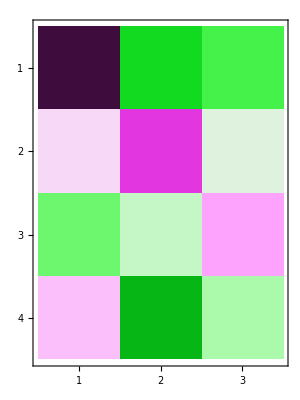

```mathematica
data["X"];
data["Y"];
(A=PLSR[%%,%,4])//MatrixForm
MatrixPlot[%,ColorFunction->"GreenPinkTones"]
```

#### analysis

```mathematica
A
```

{{0.198129,-0.0559291,-0.0296899},{9.16134×10^-7,0.0938074,-1.30876×10^-7},{-0.0224005,-3.81238×10^-7,0.00320008},{6.65294×10^-6,-0.0651732,-9.50421×10^-7}}

```mathematica
MatrixRank[A[[{1,2,3,4},All]]]
```

3

```mathematica
Solve[{1,x1,x2,x3}.A=={0,0,0}]
Solve[{1,x1,x2,0}.A[[All,{1,2}]]=={0,0}]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{6.65294×10^-6,-0.0224005,9.16134×10^-7,0.198129},{-0.0651732,-3.81238×10^-7,0.0938074,-0.0559291},{-9.50421×10^-7,0.00320008,-1.30876×10^-7,-0.0296899}} may contain significant numerical errors.

{{x1→2.53679×10^11,x2→1.1882×10^8,x3→3.65135×10^11}}

{{x1→0.596248,x2→8.84485}}

#### tables

```mathematica
Grid[Join[Transpose@{Join[{"","const"},data["names"]]},Join[{data["names"]},A],2],Frame->All]
```

| Эпителиальные клетки | Патологический микрорганизм | Антагонистичный (противопатологический организм)
const | 0.198129 | -0.0559291 | -0.0296899
Эпителиальные клетки | 9.16134×10^-7 | 0.0938074 | -1.30876×10^-7
Патологический микрорганизм | -0.0224005 | -3.81238×10^-7 | 0.00320008
Антагонистичный (противопатологический организм) | 6.65294×10^-6 | -0.0651732 | -9.50421×10^-7

```mathematica
Grid[Join[Transpose@{Join[{"","const"},data["names"]]},Join[{data["names"]},Transpose@kmConfidenceInterval[data["X"],data["Y"],A]],2],Frame->All]
```

| Эпителиальные клетки | Патологический микрорганизм | Антагонистичный (противопатологический организм)
const | 0.19813 (±0.000258) | -0.05593 (±0.000273) | -0.02969 (±0.0000368)
Эпителиальные клетки | 0.00000 (±4.29×10^-6) | 0.09381 (±4.54×10^-6) | -0.00000 (±6.13×10^-7)
Патологический микрорганизм | -0.02240 (±3.88×10^-7) | -0.00000 (±4.11×10^-7) | 0.00320 (±5.54×10^-8)
Антагонистичный (противопатологический организм) | 0.00001 (±0.0000221) | -0.06517 (±0.0000234) | -0.00000 (±3.16×10^-6)

```mathematica
{"Эпителиальные клетки X", "Кандида Y","Бактерии стрептококков Z"};
Grid[Join[Transpose@{Join[{"","const"},%]},Join[{%},A],2],Frame->All]
```

| Эпителиальные клетки X | Кандида Y | Бактерии стрептококков Z
const | 0.198129 | -0.0559291 | -0.0296899
Эпителиальные клетки X | 9.16134×10^-7 | 0.0938074 | -1.30876×10^-7
Кандида Y | -0.0224005 | -3.81238×10^-7 | 0.00320008
Бактерии стрептококков Z | 6.65294×10^-6 | -0.0651732 | -9.50421×10^-7

```mathematica
Join[A,Table[StringForm["a_(``, ``)",i,j],{i,0,3},{j,1,3}],2][[All,{4,1,5,2,6,3}]];
{"Эпителиальные клетки X", "Кандида Y","Бактерии стрептококков Z"};
Grid[Join[Transpose@{Join[{"","const"},%]},Join[{Riffle[%,SpanFromLeft,{2,-1,2}]},%%],2],Frame->All]
```

| Эпителиальные клетки X |  | Кандида Y |  | Бактерии стрептококков Z | 
const | a_(RowBox[{) | 0.198129 | a_(RowBox[{) | -0.0559291 | a_(RowBox[{) | -0.0296899
Эпителиальные клетки X | a_(RowBox[{) | 9.16134×10^-7 | a_(RowBox[{) | 0.0938074 | a_(RowBox[{) | -1.30876×10^-7
Кандида Y | a_(RowBox[{) | -0.0224005 | a_(RowBox[{) | -3.81238×10^-7 | a_(RowBox[{) | 0.00320008
Бактерии стрептококков Z | a_(RowBox[{) | 6.65294×10^-6 | a_(RowBox[{) | -0.0651732 | a_(RowBox[{) | -9.50421×10^-7

```mathematica
Join[Transpose@kmConfidenceInterval[data["X"],data["Y"],A],Table[StringForm["a_(``, ``)",i,j],{i,0,3},{j,1,3}],2][[All,{4,1,5,2,6,3}]];
{"Эпителиальные клетки X", "Кандида Y","Бактерии стрептококков Z"};
Grid[Join[Transpose@{Join[{"","Естественный рост"},%]},Join[{Riffle[%,SpanFromLeft,{2,-1,2}]},%%],2],Frame->All,Alignment->{{Center},{Left}}]
(*Export["./Documents/Thesis/res/smoothed-trapez.png",%]*)
```

| Эпителиальные клетки X |  | Кандида Y |  | Бактерии стрептококков Z | 
Естественный рост | a_(RowBox[{) | 0.19813 (±0.000258) | a_(RowBox[{) | -0.05593 (±0.000273) | a_(RowBox[{) | -0.02969 (±0.0000368)
Эпителиальные клетки X | a_(RowBox[{) | 0.00000 (±4.29×10^-6) | a_(RowBox[{) | 0.09381 (±4.54×10^-6) | a_(RowBox[{) | -0.00000 (±6.13×10^-7)
Кандида Y | a_(RowBox[{) | -0.02240 (±3.88×10^-7) | a_(RowBox[{) | -0.00000 (±4.11×10^-7) | a_(RowBox[{) | 0.00320 (±5.54×10^-8)
Бактерии стрептококков Z | a_(RowBox[{) | 0.00001 (±0.0000221) | a_(RowBox[{) | -0.06517 (±0.0000234) | a_(RowBox[{) | -0.00000 (±3.16×10^-6)

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["./Documents/Thesis/res/smoothed-trapez.png"]]]
```

#### system

```mathematica
DecimalForm[Thread[Rule[Flatten@Table[StringForm["a_(````)",i,j],{i,0,3},{j,1,3}],Flatten@A]],{3,3}]
```

{SubscriptBox[a, RowBox[{"\"0\""}]RowBox[{"\"1\""}]]→0.198,SubscriptBox[a, RowBox[{"\"0\""}]RowBox[{"\"2\""}]]→-0.056,SubscriptBox[a, RowBox[{"\"0\""}]RowBox[{"\"3\""}]]→-0.030,SubscriptBox[a, RowBox[{"\"1\""}]RowBox[{"\"1\""}]]→0.000,SubscriptBox[a, RowBox[{"\"1\""}]RowBox[{"\"2\""}]]→0.094,SubscriptBox[a, RowBox[{"\"1\""}]RowBox[{"\"3\""}]]→-0.000,SubscriptBox[a, RowBox[{"\"2\""}]RowBox[{"\"1\""}]]→-0.022,SubscriptBox[a, RowBox[{"\"2\""}]RowBox[{"\"2\""}]]→-0.000,SubscriptBox[a, RowBox[{"\"2\""}]RowBox[{"\"3\""}]]→0.003,SubscriptBox[a, RowBox[{"\"3\""}]RowBox[{"\"1\""}]]→0.000,SubscriptBox[a, RowBox[{"\"3\""}]RowBox[{"\"2\""}]]→-0.065,SubscriptBox[a, RowBox[{"\"3\""}]RowBox[{"\"3\""}]]→-0.000}

Piecewise[{{ⅆX/ⅆt=X(0.198                        -0.022"""Y), }, {ⅆY/ⅆt=Y(-0.056 "" +0.094X                     -0.065 Z), }, {ⅆZ/ⅆt=Z("-0.03"                        +0.003 Y), }}]

### Сравнение

#### Решение (встроенное)

{(ⅆ X_1)/ⅆt=x_1(b_1+∑_(i=1)^3 A_(i,1)x_i)
(ⅆ x_2)/ⅆt=x_2(b_2+∑_(i=1)^3 A_(i,2)x_i)
(ⅆ x_3)/ⅆt=x_3(b_3+∑_(i=1)^3 A_(i,3)x_i)

```mathematica
NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.A),{x1[0],x2[0],x3[0]}==First[preData["X"]]},{x1[t],x2[t],x3[t]},{t,preData["t"]//Min,1.25preData["t"]//Max}];
Nsolution=With[{$=Through[First[%[[All,All,2,0]]][#]]},$&]
```

{InterpolatingFunction[…][#1],InterpolatingFunction[…][#1],InterpolatingFunction[…][#1]}&

#### Graph

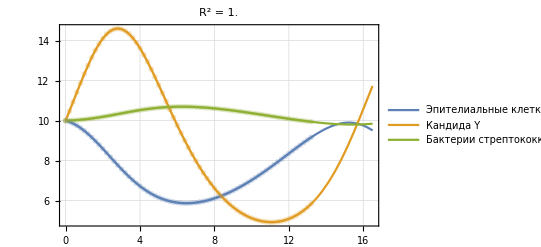

./Documents/Thesis/res/smoothed-trapez-plot.png

```mathematica
Show[
Plot[Evaluate[Nsolution[t]],{t,preData["t"]//Min,1.25preData["t"]//Max},PlotRange->{{0,All},{0,All}},Frame->True,GridLines->Automatic,PlotLegends->{"Эпителиальные клетки X", "Кандида Y","Бактерии стрептококков Z"},PlotStyle->Directive[Thick]],
ListPlot[Transpose[preData["X"][[;;;;5]]],PlotMarkers->{"OpenMarkers"},PlotStyle->Opacity[.3],
DataRange->{0,Last[preData["t"]]},Joined->True],
PlotLabel->StringForm["R^2 = ``",Mean[kmCoefficientR2Raw[Nsolution,Transpose@preData["X"],preData["t"]]]]
]
Export["./Documents/Thesis/res/smoothed-trapez-plot.png",%]
```

```mathematica
kmCoefficientR2[data["X"],data["Y"],A]
kmCoefficientR2Raw[Nsolution,Transpose@preData["X"],preData["t"]]
```

{1.,1.,1.}

{1.,1.,1.}

#### NsolutionInfty

{InterpolatingFunction[…][#1],InterpolatingFunction[…][#1],InterpolatingFunction[…][#1]}&

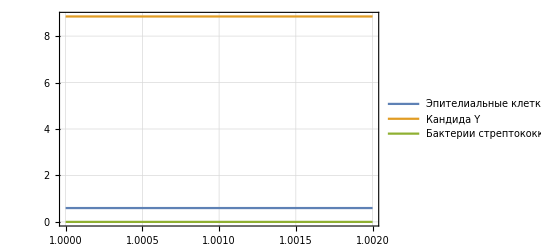

```mathematica
NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.A),{x1[0],x2[0],x3[0]}==First[preData["X"]]},{x1[t],x2[t],x3[t]},{t,10^7,1.002 10^7}];
NsolutionInfty=With[{$=Through[First[%[[All,All,2,0]]][#]]},$&]
Plot[Evaluate[NsolutionInfty[t]],{t,10^7,1.002 10^7},PlotRange->{{10^7,1.002 10^7},{0,All}},Frame->True,GridLines->Automatic,PlotStyle->Directive[Thick],PlotLegends->{"Эпителиальные клетки X", "Кандида Y","Бактерии стрептококков Z"}]
```

Piecewise[{{ⅆX/ⅆt=X(0.198                        -0.022"""Y), }, {ⅆY/ⅆt=Y(-0.056 "" +0.094X                     -0.065 Z), }, {ⅆZ/ⅆt=Z("-0.03"                        +0.003 Y), }}]

X=0.6
Y=8.8
Z=0.0

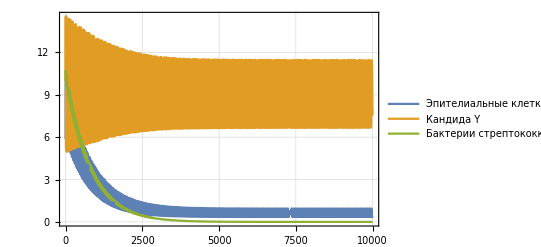

./Documents/Thesis/res/smoothed-trapez-semiinfty.png

```mathematica
NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.A),{x1[0],x2[0],x3[0]}==First[preData["X"]]},{x1[t],x2[t],x3[t]},{t,0.,1. 10^4}];
NsolutionInfty=With[{$=Through[First[%[[All,All,2,0]]][#]]},$&];
Plot[Evaluate[NsolutionInfty[t]],{t,0,1. 10^4},PlotRange->{{0,All},{0,All}},Frame->True,GridLines->Automatic,PlotStyle->Directive[Thick],PlotLegends->{"Эпителиальные клетки X", "Кандида Y","Бактерии стрептококков Z"}]
Export["./Documents/Thesis/res/smoothed-trapez-semiinfty.png",%]
```

```mathematica
(*NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.A),{x1[0],x2[0],x3[0]}==First[preData["X"]]},{x1[t],x2[t],x3[t]},{t,0.,1. 10^7}];
NsolutionInfty=With[{$=Through[First[%[[All,All,2,0]]][#]]},$&];
Plot[Evaluate[NsolutionInfty[t]],{t,0,1. 10^7},PlotRange->{{0,All},{0,All}},Frame->True,GridLines->Automatic,PlotStyle->Directive[Thick],PlotLegends->{"Эпителиальные клетки X", "Кандида Y","Бактерии стрептококков Z"}]*)
```

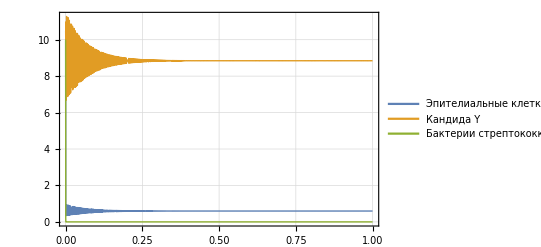

```mathematica
NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.A),{x1[0],x2[0],x3[0]}==First[preData["X"]]},{x1[t],x2[t],x3[t]},{t,1. 10^7,1. 10^7}];
NsolutionInfty=With[{$=Through[First[%[[All,All,2,0]]][#]]},$&];
NsolutionInfty[1. 10^7]
```

{0.596205,8.84514,4.7×10^-322}